This is File S1 from Lohse et al. 2016

# Estimating divergence and gene flow

This file gives an overview of the methodology, and defines all necessary functions.  “Evaluate intialisation” to set up the functions.  Examples are given in separate notebooks.  There is also an index file that notes changes between versions, and changes that are still to be implemented.

### Overview

#### Generating functions for IM models

We show how to derive the probability of mutational configurations, defined as counts of the various types of mutation in non-recombining blocks.  The general method is described by Lohse et al. (2011).  A wide variety of isolation-with-migration models can be fitted, including splits of ancestral populations into different demes, different population sizes between demes, steady migration between demes, admixture events, changes in population size through time, and bottlenecks.  A generating function (GF) is calculated for the model; this is a function of the model parameters, and of a set of dummy variables ω_S that correspond to the lengths of all possible branches.  Differentiating wrt the ω_S gives the probability of each mutational configuration, and the probabilities of all configurations can be tabulated from the coefficients of a series expansion in the ω_S.  The probability of observing various configurations across a large number of blocks is then found by multiplying across this table.

#### Speeding up the calculations

A direct calculation of the table of probabilities is not feasible for more than two or three sampled genomes.  Here, we implement some computational tricks that make the calculations feasible for larger samples and more elaborate models.  Exact calculations are still only feasible for small samples (up to ~ 6 genomes, say); we do not consider here approximate methods that could be used with larger samples.

The general strategy is to initially automatically generate the GF of the rooted genealogies with unique labels for all individuals. We then make use of symmetries (i.e. where genes sampled from the same population are exchangeable) by conditioning on a single random labeling per equivalence class, noting that the full GF can be written as a sum of the GFs of such class representatives. To remove phase and outgroup information, we combine all branch variables that contribute to each of the site types.

Tricks include:
	- separating the GF into a sum over the possible topologies
	- separating topologies into classes that are equivalent, and only calculating one term in each class
	- treating unrooted or unphased diploid data, and merging equivalent branches
	- calculating the probabilities of mutational configurations using a series expansion of the GF
	- tabulating numbers of mutations only up to some maximum number, and then finding the residual probability
	- choosing an appropriate algorithm to maximise the likelihood, and using numerical rather than symbolic expressions
We emphasise that these computational tricks do not affect the probabilities, which are still calculated exactly.

This notebook contains two sets of functions. The first set calculates a generating function under a wide variety of models; this is a function of a set of dummy variables, ω[], which correspond to all the possible branch lengths in the genealogy.  The second set use this GF to compile a table of probabilities of the various mutational configurations.  The GF is also a function of the model parameters, but this does not affect the calculation of mutational configurations, which is independent of the evolutionary model.

#### Extensions

We illustrate these methods using some simple models, elaborated in separate notebooks. However, the same code can be used for a wide variety of IM models, with arbitrary numbers of demes, varying population size, population splits, and so on.  The limiting factor is that numerical maximisation is slow with large numbers of parameters, and there will in any case be limited statistical power to estimate multiple parameters.

Lohse et al. (2011) show how the GF can be calculated for multiple loci; this is implemented in the Supplementary Notebook that accompanies that paper.  We have not included that case here, because the number of mutational configurations that must be tabulated is daunting, and because it is not clear how best to make inferences from data from linked loci.

#### Using Mathematica

The notebook uses some compact Mathematica notation for applying rules to expressions (expr/.rules), for mapping functions onto lists of expressions (f/@{x_1,…}), and for defining “pure functions (e.g. (#^2)&).  Documentation can be found using ?f; there is a useful summary in Tips.nb.

To set up the notebook, “Evaluate initialisation”.  Variables and functions that have already been defined appear in black, whilst those not yet defined are in blue. To find information about a function f, type ?f and enter.

Comments and explanations are hidden within subsections - double click cell brackets at right to open these.  To find information about a function, use ?name and evaluate.  There are also notes and examples associated with each function definition in the following section.

## Definitions

### Elementary functions

#### TakeAway

```mathematica
TakeAway::usage = "TakeAway[U,V]  gives the set U, minus elements V. Note that this is not the same as Complement[U,V] if U contains repeated elements. ";
```

```mathematica
TakeAway[U_List, {}] := U;
TakeAway[U_List, {v_}] := Drop[U, Cases[Position[U, v],{_Integer}]⟦1⟧] /; Complement[{v}, U] == {};
TakeAway[U_List, V_List] := TakeAway[TakeAway[U, Take[V, 1]], Drop[V, 1]] /; Complement[V, U] == {};
TakeAway[U_List, W__List, V_List] := TakeAway[TakeAway[U, W], V];
```

Example:

This takes just one element c from the list:

```mathematica
TakeAway[{a,b,c,c,d},{c}]
```

{a,b,c,d}

This takes away both elements, in effect wrapping Union[] around the arguments

```mathematica
Complement[{a,b,c,c,d},{c}]
```

{a,b,d}

#### TopologyQ

```mathematica
TopologyQ::usage="TopologyQ[lineages,topology] tests whether a set of lineages is consistent with a given topology.  For example, {{a,b},{c},{d}} is consistent with {{{a,b},c},d}, but {{a,d},{b},{c}} is not.  This simply checks that each set of lineages is included in PossibleSets[tp]. TopologyQ[lineages,All] returns True.";
```

```mathematica
TopologyQ[ln_List,All]:=True;
TopologyQ[ln_List,tp_List]:=Module[{ps=PossibleSets[tp]},
And@@(MemberQ[ps,#]&/@DeleteCases[ln,{_}])];
```

Note: There is s subtlety to the notation.  A set of lineages is a list of lists, where each element gives the set of genes to which the lineage is ancestral - here, {{c},{a,b}}, for example; the first element, {c}, represents a lineage ancestral to a single gene, c, for example.  In contrast, a topology is a grouping of genes - for example, {{a,b},c}, with c appearing, not {c}

#### PossibleSets

```mathematica
PossibleSets::usage="PossibleSets[topology] stores the possible sets of lineages that are consistent with the given topology.  The topology is represented as a nested list.   With n leaves, and a bifurcating tree, there are n-2 possible sets (not counting single leaves).  Leaves must not themselves be lists.";
```

```mathematica
PossibleSets[tp_List]:=PossibleSets[tp]=Sort[Append[Sort/@(Flatten/@(Extract[tp,Drop[#,-1]]&/@DeleteCases[Position[tp,List],{0}])),Sort[Flatten[tp]]]];
```

Example: Only these three lineages are consistent with this topology - others, such as {b,c}, are not.  Note that {e} is not included.

```mathematica
PossibleSets[{{a,b},{c,d},e}]
```

{{a,b},{c,d},{a,b,c,d,e}}

If one writes {e} as a list (i.e. a lineage ancestral to e).  then {e} is included.

```mathematica
PossibleSets[{{a,b},{c,d},{e}}]
```

{{e},{a,b},{c,d},{a,b,c,d,e}}

#### NumberInClass

```mathematica
NumberInClass::usage="NumberInClass[{a,a,b,c,c}] gives the number of topologies in each of the classes defined by Topologies[{a,a,b,c,c}].  This works by simple enumeration, and so may be slow for large sets.";
```

```mathematica
NumberInClass::badMatch="The order of the topologies is `1`, which does not match Topologies[`2`]";
```

```mathematica
NumberInClass[s_List]:=Module[{a,ds,n=Length[s],res},
ds=Array[a,n];
res=Transpose[Tally[FullSort/@(Topologies[ds]/.{a[j_]:>s⟦j⟧})]];
If[Not[res⟦1⟧==Topologies[s]],Message[NumberInClass::badMatch,res⟦1⟧,s]];
res⟦2⟧];
```

Example: There are 35 classes of topology connecting {a,a,b,c,c}, and a total of 105 possible topologies in all:

```mathematica
Transpose[{Topologies[{a,a,b,c,c}],NumberInClass[{a,a,b,c,c}]}]
```

{{{a,{a,{b,{c,c}}}},2},{{a,{a,{c,{b,c}}}},4},{{a,{b,{a,{c,c}}}},2},{{a,{b,{c,{a,c}}}},4},{{a,{c,{a,{b,c}}}},4},{{a,{c,{b,{a,c}}}},4},{{a,{c,{c,{a,b}}}},4},{{a,{{a,b},{c,c}}},2},{{a,{{a,c},{b,c}}},4},{{b,{a,{a,{c,c}}}},2},{{b,{a,{c,{a,c}}}},4},{{b,{c,{a,{a,c}}}},4},{{b,{c,{c,{a,a}}}},2},{{b,{{a,a},{c,c}}},1},{{b,{{a,c},{a,c}}},2},{{c,{a,{a,{b,c}}}},4},{{c,{a,{b,{a,c}}}},4},{{c,{a,{c,{a,b}}}},4},{{c,{b,{a,{a,c}}}},4},{{c,{b,{c,{a,a}}}},2},{{c,{c,{a,{a,b}}}},4},{{c,{c,{b,{a,a}}}},2},{{c,{{a,a},{b,c}}},2},{{c,{{a,b},{a,c}}},4},{{{a,a},{b,{c,c}}},1},{{{a,a},{c,{b,c}}},2},{{{a,b},{a,{c,c}}},2},{{{a,b},{c,{a,c}}},4},{{{a,c},{a,{b,c}}},4},{{{a,c},{b,{a,c}}},4},{{{a,c},{c,{a,b}}},4},{{{a,{a,b}},{c,c}},2},{{{a,{a,c}},{b,c}},4},{{{b,c},{c,{a,a}}},2},{{{b,{a,a}},{c,c}},1}}

```mathematica
{Length[NumberInClass[{a,a,b,c,c}]],Total[NumberInClass[{a,a,b,c,c}]]}
```

{35,105}

#### Topologies

Given a set of genes, {a,a,b,c,c,…}, some of which are equivalent, I would like to find all distinct bifurcating topologies that connect them.  I do this by working back, coalescence by coalescence, until there is just one pair remaining.

```mathematica
Topologies::usage="Topologies[{a,b,c,d}] lists all the distinct topologies, represented as nested lists";
```

```mathematica
Topologies[x_List]:=First/@NestWhile[Union[Flatten[Coalesce/@#,1]]&,{x},Union[Length/@#]≠{1}&];
```

Example:  There are only 3 kinds of topology that can connect 5 equivalent genes

```mathematica
Topologies[{a,a,a,a,a}]
```

{{a,{a,{a,{a,a}}}},{a,{{a,a},{a,a}}},{{a,a},{a,{a,a}}}}

There are 35 classes of topology that can connect genes {a,a,b,c,c}:

```mathematica
Topologies[{a,a,b,c,c}]
```

{{a,{a,{b,{c,c}}}},{a,{a,{c,{b,c}}}},{a,{b,{a,{c,c}}}},{a,{b,{c,{a,c}}}},{a,{c,{a,{b,c}}}},{a,{c,{b,{a,c}}}},{a,{c,{c,{a,b}}}},{a,{{a,b},{c,c}}},{a,{{a,c},{b,c}}},{b,{a,{a,{c,c}}}},{b,{a,{c,{a,c}}}},{b,{c,{a,{a,c}}}},{b,{c,{c,{a,a}}}},{b,{{a,a},{c,c}}},{b,{{a,c},{a,c}}},{c,{a,{a,{b,c}}}},{c,{a,{b,{a,c}}}},{c,{a,{c,{a,b}}}},{c,{b,{a,{a,c}}}},{c,{b,{c,{a,a}}}},{c,{c,{a,{a,b}}}},{c,{c,{b,{a,a}}}},{c,{{a,a},{b,c}}},{c,{{a,b},{a,c}}},{{a,a},{b,{c,c}}},{{a,a},{c,{b,c}}},{{a,b},{a,{c,c}}},{{a,b},{c,{a,c}}},{{a,c},{a,{b,c}}},{{a,c},{b,{a,c}}},{{a,c},{c,{a,b}}},{{a,{a,b}},{c,c}},{{a,{a,c}},{b,c}},{{b,c},{c,{a,a}}},{{b,{a,a}},{c,c}}}

```mathematica
Topologies[{a,a,b,c,c}]//Length
```

35

#### Checking Topologies[]

This table gives the number of classes of topology that connect n distinct genes; n genes divided evenly into two classes (e.g. two demes); and n equivalent genes:

```mathematica
Prepend[Table[{j,Length[Topologies[Array[Subscript[a, #]&,j]]],Length[Topologies[Join[ConstantArray[Subscript[a, 1],Quotient[j,2]],ConstantArray[Subscript[a, 2],j-Quotient[j,2]]]]],Length[Topologies[ConstantArray[a,j]]]},{j,2,8}],{"n","unranked","EC 2 pops","EC 1 pop"}]//TableForm
```

n | unranked | EC 2 pops | EC 1 pop
2 | 1 | 1 | 1
3 | 3 | 2 | 1
4 | 15 | 6 | 2
5 | 105 | 15 | 3
6 | 945 | 49 | 6
7 | 10395 | 155 | 11
8 | 135135 | 560 | 23

The calculation is done by using n distinct genes; n genes divided equally into two types; and n equivalent genes:

```mathematica
{Array[Subscript[a, #]&,5],Join[ConstantArray[Subscript[a, 1],Quotient[5,2]],ConstantArray[Subscript[a, 2],5-Quotient[5,2]]],ConstantArray[a,5]}
```

{{a_1,a_2,a_3,a_4,a_5},{a_1,a_1,a_2,a_2,a_2},{a,a,a,a,a}}

This is the table from the paper:

#### FullSort

```mathematica
FullSort::usage="FullSort[topology] sorts the topology into the standard order. (For obscure reasons, //.{{f_,g_}:>Sort[{f,g}] does not acheive this)";
```

```mathematica
FullSort[xx_List]:=Module[{j,yy},
yy=xx;
Do[yy=Replace[yy,{{f_,g_}:>Sort[{f,g}]},j],{j,Depth[xx]}];Sort[yy]];
```

### Functions used to generate the equations for the GF

#### TotalRate

```mathematica
TotalRate::usage="TotalRate[{{{a},{b},{c}},{{d},{e}},…},{{x},{y},…}] gives the total rate of events for a given configuration of leaves. Coalescence→λ gives coalescence at rate λ[{x}] in deme {x}. Migration->M represents migrationat rate M[{x},{y}] from population {x} to {y}, forwards in time.   Splits→Λ represents splitting of a population {{x},{y}} into separate demes at rate Λ[{{x},{y}}]. Note that M=4Nm, whereas Λ=2Nλ. Admixture->{{A,a},…} represents admixture events at rate A, and similarly for Bottlenecks→{{B,b},…}, ChangeMigration→{{dM,M},…} and ChangeCoalescence->{{dλ,λ},…}. Throughout, both lineages and demes must be represented as lists, so that they can be merged. Deme labels {{x},{y}…} must not contain repeated elements. TotalRate[{{a},{b},{c}}] applies to a single population, and takes options Coalescence, ChangeCoalescence and Bottlenecks. Note:  with a single deme, option arguments must be functions.  For example, Coalescence→λ will generate rates λ[] in a single deme, and λ[{x}] in deme {x}.";
```

```mathematica
Options[TotalRate]={Coalescence->(1&),Migration->(0&),Splits->(0&),Admixture->{},Bottlenecks->{},ChangeMigration->{},ChangeCoalescence->{}};
```

```mathematica
TotalRate[xx_List,opts___Rule]:=Module[{nn=Length[xx] (*number of lineages*),
λ=Coalescence/.{opts}/.Options[TotalRate],
dλλ=ChangeCoalescence/.{opts}/.Options[TotalRate],
Bb=Bottlenecks/.{opts}/.Options[TotalRate]},
(nn(nn-1))/2 λ[]+If[dλλ=={},0,dλλ⟦1,1⟧[]]+If[Bb=={},0,Bb⟦1,1⟧[]](*total rate of coalescence, bottlenecks and changes in coalescence rate *)];
```

```mathematica
TotalRate[xx_List,dl_List,opts___Rule]:=Module[{nn=Length/@xx (*lists number of lineages within each deme*),
λ=Coalescence/.{opts}/.Options[TotalRate],
M=Migration/.{opts}/.Options[TotalRate],
Λ=Splits/.{opts}/.Options[TotalRate],
Aa=Admixture/.{opts}/.Options[TotalRate],
dmm=ChangeMigration/.{opts}/.Options[TotalRate],
dλλ=ChangeCoalescence/.{opts}/.Options[TotalRate],
Bb=Bottlenecks/.{opts}/.Options[TotalRate]},
Total[Λ/@Subsets[dl,{2}]](* rate of splits between each pair of demes*)
+(((nn(nn-1))/2).(λ/@dl))(*total rate of coalescence within demes*)
+1/2 Total[Outer[M,dl,dl,1].nn/.M[a_,a_]->0]
(*sum of all pairwise migration rates, weighted by # of lineages in the deme that receives migrants*)
+If[Bb=={},0,Total[Bb⟦1,1⟧/@dl]] (* total rate of bottlenecks *)
+If[dλλ=={},0,Total[dλλ⟦1,1⟧/@dl]] (* total rate of changes in coalescence rate *)
+If[dmm=={},0,Total[Outer[dmm⟦1,1⟧,dl,dl,1]/.dmm⟦1,1⟧[a_,a_]->0,2] ](* total rate of changes in migration rate *)
+If[Aa=={},0,Total[Outer[Aa⟦1,1⟧,dl,dl,1]/.Aa⟦1,1⟧[a_,a_]->0,2]] (* total rate of admixture *)];
```

Note: Each M is weighted by the total number of lineages in the deme that receives migrants. Empty demes can contribute migrants: tracing back in time, lineages move out into that empty deme.  Bottlenecks, admixture, and changes in migration or coalescence rate are not weighted by the number of lineages.

Example: For a single deme, the default is a coalescence rate of λ=1. With three lineages, the total rate is 3:

```mathematica
TotalRate[{{a},{b},{c}}]
```

3

The coalescence rate can be specified, as well as the rate of bottlenecks and of changes in coalescence rate.  Note that these are given as functions λ[] etc:

```mathematica
TotalRate[{{a},{b},{c}},Coalescence->λ,Bottlenecks->{{Subscript[B, 1],Subscript[b, 1]},{Subscript[B, 2],Subscript[b, 2]}},ChangeCoalescence->{{dλ,λ}}]
```

dλ[]+3 λ[]+B_1[]

Example: There are 3 demes, with 3, 2, 0 lineages respectively.  By default, the coalescence rate is 1 in all demes, and the total rate of coalescence is 3+1=4:

```mathematica
TotalRate[{{{a},{b},{c}},{{d},{e}},{}},{{x},{y},{z}}]
```

4

Example: There are three split rates, and 6 migration rates.  Demes x, y, z have 3, 2, 0 lineages, respectively, and so the total rate of migration is weighted by the numbers in the receiving deme:

```mathematica
TotalRate[{{{a},{b},{c}},{{d},{e}},{}},{{x},{y},{z}},Coalescence->λ,Migration->M,Splits->Λ]
```

1/2 (2 M[{x},{y}]+3 M[{y},{x}]+3 M[{z},{x}]+2 M[{z},{y}])+3 λ[{x}]+λ[{y}]+Λ[{{x},{y}}]+Λ[{{x},{z}}]+Λ[{{y},{z}}]

Bottlenecks and changes in coalescence rate can be specified for each deme.  These are not weighted by he numbers of lineages:

```mathematica
TotalRate[{{{a},{b},{c}},{{d},{e}},{}},{{x},{y},{z}},Bottlenecks->{{B,b}},ChangeCoalescence->{{dλ,λ}}]
```

4+B[{x}]+B[{y}]+B[{z}]+dλ[{x}]+dλ[{y}]+dλ[{z}]

Similarly, admixture and changes in migration can be specified for each pair of demes:

```mathematica
TotalRate[{{{a},{b},{c}},{{d},{e}},{}},{{x},{y},{z}},Admixture->{{A,a}},ChangeMigration->{{Subscript[dM, 1],Subscript[M, 1]}}]
```

4+A[{x},{y}]+A[{x},{z}]+A[{y},{x}]+A[{y},{z}]+A[{z},{x}]+A[{z},{y}]+dM_1[{x},{y}]+dM_1[{x},{z}]+dM_1[{y},{x}]+dM_1[{y},{z}]+dM_1[{z},{x}]+dM_1[{z},{y}]

#### Mergers

```mathematica
Mergers::usage"Mergers[{{a},{b},{c}}] or Mergers[{{a},{b},{c}},All] returns a list of all pairwise coalescences between these lineages. Mergers[{{a},{b},{c}},{{a,b},c}] only permits mergers consistent with the topology {{a,b},c}} - in this example, only {{a,b},c}}. Mergers[k,{{a},{b},{c}}] or Mergers[k,{{a},{b},{c}},topology] lists all possible results of k coalescence events; this list may contain repeated elements,if there are multiple paths to the same configuration. An error is returned if the list itself is inconsistent with the topology. Lineages must be represented as lists.";
```

```mathematica
Mergers::badList="Lineages `1` are not consistent with the topology `2`";
```

```mathematica
Mergers[xl:{___List}]:=Sort[Prepend[DeleteCases[DeleteCases[xl,#⟦1⟧,1,1],#⟦2⟧,1,1],Sort[Flatten[#,1]]]]&/@Subsets[xl,{2}];
```

```mathematica
Mergers[xl:{___List},All]:=Mergers[xl];
Mergers[xl:{___List},tp_List]:=If[TopologyQ[xl,tp],
Select[Mergers[xl],TopologyQ[#,tp]&],
Message[Mergers::badList,xl,tp];{}];
```

```mathematica
Mergers[0,xl:{___List}]:={xl};
Mergers[1,xl:{___List}]:=Mergers[xl];
Mergers[k_Integer,xl:{___List}]:=Flatten[Mergers/@Mergers[k-1,xl],1];
```

```mathematica
Mergers[k_Integer,xl:{___List},All]:=Mergers[k,xl];
Mergers[0,xl:{___List},tp_List]:=If[TopologyQ[xl,tp],{xl},Message[Mergers::badList,xl,tp];{}];
Mergers[1,xl:{___List},tp_List]:=Mergers[xl,tp];
Mergers[k_Integer,xl:{___List},tp_List]:=If[TopologyQ[xl,tp],
Flatten[Mergers[#,tp]&/@Mergers[k-1,xl,tp],1],
Message[Mergers::badList,xl,tp];{}];
```

Example: There are three ways to merge three lineages:

```mathematica
Mergers[{{a},{b},{c}}]
```

{{{c},{a,b}},{{b},{a,c}},{{a},{b,c}}}

Only one of these is consistent with the topology {{a,b},c}:

```mathematica
Mergers[{{a},{b},{c}},{{a,b},c}]
```

{{{c},{a,b}}}

Example : There are 180 ways in which 3 coalescences can occur amongst 5 lineages:

```mathematica
Mergers[3,{{a},{b},{c},{d},{e}}]
```

{{{c,d},{a,b,e}},{{a,b},{c,d,e}},{{e},{a,b,c,d}},{{c,e},{a,b,d}},{{a,b},{c,d,e}},{{d},{a,b,c,e}},{{d,e},{a,b,c}},{{e},{a,b,c,d}},{{d},{a,b,c,e}},{{d,e},{a,b,c}},{{a,b},{c,d,e}},{{c},{a,b,d,e}},{{c,e},{a,b,d}},{{e},{a,b,c,d}},{{c},{a,b,d,e}},{{c,d},{a,b,e}},{{d},{a,b,c,e}},{{c},{a,b,d,e}},{{b,d},{a,c,e}},{{a,c},{b,d,e}},{{e},{a,b,c,d}},{{b,e},{a,c,d}},{{a,c},{b,d,e}},{{d},{a,b,c,e}},{{d,e},{a,b,c}},{{e},{a,b,c,d}},{{d},{a,b,c,e}},{{d,e},{a,b,c}},{{a,c},{b,d,e}},{{b},{a,c,d,e}},{{b,e},{a,c,d}},{{e},{a,b,c,d}},{{b},{a,c,d,e}},{{b,d},{a,c,e}},{{d},{a,b,c,e}},{{b},{a,c,d,e}},{{b,c},{a,d,e}},{{a,d},{b,c,e}},{{e},{a,b,c,d}},{{b,e},{a,c,d}},{{a,d},{b,c,e}},{{c},{a,b,d,e}},{{c,e},{a,b,d}},{{e},{a,b,c,d}},{{c},{a,b,d,e}},{{c,e},{a,b,d}},{{a,d},{b,c,e}},{{b},{a,c,d,e}},{{b,e},{a,c,d}},{{e},{a,b,c,d}},{{b},{a,c,d,e}},{{b,c},{a,d,e}},{{c},{a,b,d,e}},{{b},{a,c,d,e}},{{b,c},{a,d,e}},{{a,e},{b,c,d}},{{d},{a,b,c,e}},{{b,d},{a,c,e}},{{a,e},{b,c,d}},{{c},{a,b,d,e}},{{c,d},{a,b,e}},{{d},{a,b,c,e}},{{c},{a,b,d,e}},{{c,d},{a,b,e}},{{a,e},{b,c,d}},{{b},{a,c,d,e}},{{b,d},{a,c,e}},{{d},{a,b,c,e}},{{b},{a,c,d,e}},{{b,c},{a,d,e}},{{c},{a,b,d,e}},{{b},{a,c,d,e}},{{b,c},{a,d,e}},{{a,d},{b,c,e}},{{e},{a,b,c,d}},{{b,c},{a,d,e}},{{a,e},{b,c,d}},{{d},{a,b,c,e}},{{d,e},{a,b,c}},{{e},{a,b,c,d}},{{d},{a,b,c,e}},{{d,e},{a,b,c}},{{b,c},{a,d,e}},{{a},{b,c,d,e}},{{a,e},{b,c,d}},{{e},{a,b,c,d}},{{a},{b,c,d,e}},{{a,d},{b,c,e}},{{d},{a,b,c,e}},{{a},{b,c,d,e}},{{b,d},{a,c,e}},{{a,c},{b,d,e}},{{e},{a,b,c,d}},{{b,d},{a,c,e}},{{a,e},{b,c,d}},{{c},{a,b,d,e}},{{c,e},{a,b,d}},{{e},{a,b,c,d}},{{c},{a,b,d,e}},{{c,e},{a,b,d}},{{b,d},{a,c,e}},{{a},{b,c,d,e}},{{a,e},{b,c,d}},{{e},{a,b,c,d}},{{a},{b,c,d,e}},{{a,c},{b,d,e}},{{c},{a,b,d,e}},{{a},{b,c,d,e}},{{b,e},{a,c,d}},{{a,c},{b,d,e}},{{d},{a,b,c,e}},{{b,e},{a,c,d}},{{a,d},{b,c,e}},{{c},{a,b,d,e}},{{c,d},{a,b,e}},{{d},{a,b,c,e}},{{c},{a,b,d,e}},{{c,d},{a,b,e}},{{b,e},{a,c,d}},{{a},{b,c,d,e}},{{a,d},{b,c,e}},{{d},{a,b,c,e}},{{a},{b,c,d,e}},{{a,c},{b,d,e}},{{c},{a,b,d,e}},{{a},{b,c,d,e}},{{c,d},{a,b,e}},{{a,b},{c,d,e}},{{e},{a,b,c,d}},{{c,d},{a,b,e}},{{a,e},{b,c,d}},{{b},{a,c,d,e}},{{b,e},{a,c,d}},{{e},{a,b,c,d}},{{b},{a,c,d,e}},{{c,d},{a,b,e}},{{b,e},{a,c,d}},{{a},{b,c,d,e}},{{a,e},{b,c,d}},{{e},{a,b,c,d}},{{a},{b,c,d,e}},{{a,b},{c,d,e}},{{b},{a,c,d,e}},{{a},{b,c,d,e}},{{c,e},{a,b,d}},{{a,b},{c,d,e}},{{d},{a,b,c,e}},{{c,e},{a,b,d}},{{a,d},{b,c,e}},{{b},{a,c,d,e}},{{b,d},{a,c,e}},{{d},{a,b,c,e}},{{b},{a,c,d,e}},{{c,e},{a,b,d}},{{b,d},{a,c,e}},{{a},{b,c,d,e}},{{a,d},{b,c,e}},{{d},{a,b,c,e}},{{a},{b,c,d,e}},{{a,b},{c,d,e}},{{b},{a,c,d,e}},{{a},{b,c,d,e}},{{d,e},{a,b,c}},{{a,b},{c,d,e}},{{c},{a,b,d,e}},{{d,e},{a,b,c}},{{a,c},{b,d,e}},{{b},{a,c,d,e}},{{b,c},{a,d,e}},{{c},{a,b,d,e}},{{b},{a,c,d,e}},{{d,e},{a,b,c}},{{b,c},{a,d,e}},{{a},{b,c,d,e}},{{a,c},{b,d,e}},{{c},{a,b,d,e}},{{a},{b,c,d,e}},{{a,b},{c,d,e}},{{b},{a,c,d,e}},{{a},{b,c,d,e}}}

There are 15 distinct coalescence events, each represented 9 or 18 times:

```mathematica
Tally[Mergers[3,{{a},{b},{c},{d},{e}}]]
```

{{{{c,d},{a,b,e}},9},{{{a,b},{c,d,e}},9},{{{e},{a,b,c,d}},18},{{{c,e},{a,b,d}},9},{{{d},{a,b,c,e}},18},{{{d,e},{a,b,c}},9},{{{c},{a,b,d,e}},18},{{{b,d},{a,c,e}},9},{{{a,c},{b,d,e}},9},{{{b,e},{a,c,d}},9},{{{b},{a,c,d,e}},18},{{{b,c},{a,d,e}},9},{{{a,d},{b,c,e}},9},{{{a,e},{b,c,d}},9},{{{a},{b,c,d,e}},18}}

If we restrict to coalescence consistent with a specific topology, then there are only 3 routes to a single type of coalescence event.  These three routes correspond to three times when the {a,b} coalescence can occur, relative to the {d,e} and the {c,{d,e}} coalescences:

```mathematica
Tally[Mergers[3,{{a},{b},{c},{d},{e}},{{a,b},{c,{d,e}}}]]
```

{{{{a,b},{c,d,e}},3}}

Note: There is s subtlety to the notation.  A set of lineages is a list of lists, where each element gives the set of genes to which the lineage is ancestral - here, {{c},{a,b}}, for example; the first element, {c}, represents a lineage ancestral to a single gene, c, for example.  In contrast, a topology is a grouping of genes - for example, {{a,b},c}, with c appearing, not {c}

Note: Mergers[] with multiple coalescence is used by Bottleneck[], which finds the chance of all the possible configurations of lineages before a bottleneck

#### Coalesce

```mathematica
Coalesce::usage"Coalesce[{{a},{b},{c}}]  returns a list of all pairwise coalescences between these lineages - here, {{a},{{b},{c}}}, {{b},{{a},{c}}},{{c},{{a},{b}}}.  Similar to Mergers[], except that coalesced lineages are wrapped within a list rather than being actually merged.  Unlike Mergers[], allows for repeated elements, but does not allow restriction by topology. ";
```

```mathematica
Coalesce[xl_List]:=Sort[Prepend[TakeAway[xl,#],Sort[#]]]&/@Union[Subsets[xl,{2}]];
```

Note: This is used by Topologies[]

#### GetVars

```mathematica
GetVars::usage="GetVars[expr,ψ] lists the configurations of genes in all terms of the form ψ[ω,genes,options], GetVars[{expr,…},ψ] lists all the variables.";
```

```mathematica
GetVars[expr_,GF_]:=If[ListQ[expr],
Union[Flatten[GetVars[#,GF]&/@expr]],
Union[Extract[expr,#]&/@Position[expr,GF[_,_List,___Rule]]]];
```

#### GetConfigs

```mathematica
GetConfigs::usage="GetConfigs[expr,ψ] finds all the sets of genes that appear in terms of the form ψ[ω,{{a},{b,c}}]";
```

```mathematica
GetConfigs[expr_,ψ_]:=Union[Flatten[GetVars[expr,ψ]⟦All,2⟧,1]];
```

#### GetConfigsGF

```mathematica
GetConfigsGF::usage="GetConfigsGF[GF,ω] finds all the sets of genes that appear in terms of the form ω[{a,b}]";
```

```mathematica
GetConfigsGF[expr_,ω_]:=Union[First/@Cases[expr,ω[_List],All]];
```

#### GetVarsDemes

```mathematica
GetVarsDemes::usage="GetVarsDemes[expr,ψ] lists the configurations of genes in all terms of the form ψ[ω,genes,demes,opts], GetVarsDemes[{expr,…},ψ] lists all the variables.";
```

```mathematica
GetVarsDemes[expr_,GF_]:=If[ListQ[expr],
Union[Flatten[GetVarsDemes[#,GF]&/@expr]],
Union[Extract[expr,#]&/@Position[expr,GF[_,_List,_List,___Rule]]]];
```

#### ReduceOpts

```mathematica
ReduceOpts::usage="ReduceOpts[{opts}] reeduces the options to a standard form by removing any that are identical to the defaults Options[MakeEqns], and 
then sorting";
```

```mathematica
ReduceOpts[opts:{___Rule}]:=Sort[DeleteCases[opts,Alternatives@@Options[MakeEqns]]];
```

#### DropEventsList

```mathematica
DropEventsList::usage="DropEventsList[{opts},Bottlenecks] drops the first element {B_1,b_1} from Bottlenecks->{{B_1,b_1},…}";
```

```mathematica
DropEventsList[ol:{___Rule},e:(Bottlenecks|Admixture|ChangeMigration|ChangeCoalescence)]:=
ReduceOpts[ol/.{(e->{{_,_},x___List}):>(e->{x})}];
```

Example: This drops the first element from the list of admixture events:

```mathematica
DropEventsList[{Coalescence->λ,Bottlenecks->{{B,b}},Admixture->{{Subscript[A, 1],Subscript[a, 1]},{Subscript[A, 2],Subscript[a, 2]}}},Admixture]
```

{Coalescence→λ,Bottlenecks→{{B,b}},Admixture→{{A_2,a_2}}}

#### ChangeEventsList

```mathematica
ChangeEventsList::usage="ChangeEventsList[{opts},event,λ] drops one event from the list, and changes the corresponding parameter to λ.";
```

```mathematica
ChangeEventsList[{opts___Rule},e:(ChangeMigration|ChangeCoalescence),λ_]:=Module[{de=DropEventsList[{opts},e],e2=Switch[e,ChangeMigration,Migration,ChangeCoalescence,Coalescence,_,Null]},
ReduceOpts[If[FreeQ[de,e2],Append[de,e2->λ],de/.{(e2->_):>(e2->λ)}]]];
```

Example: One event is dropped from the list, and the corresponding parameter is changed to the new value:

```mathematica
ChangeEventsList[{ChangeCoalescence->{{Subscript[dλ, 1],Subscript[λ, 1]},{Subscript[dλ, 2],Subscript[λ, 2]}},Coalescence->Subscript[λ, 0]},ChangeCoalescence,Subscript[λ, new]]
```

{ChangeCoalescence→{{dλ_2,λ_2}},Coalescence→λ_new}

```mathematica
ChangeEventsList[{ChangeCoalescence->{{Subscript[dλ, 1],Subscript[λ, 1]},{Subscript[dλ, 2],Subscript[λ, 2]}},Bottlenecks->{{B,b}}},ChangeCoalescence,Subscript[λ, 1]]
```

{Bottlenecks→{{B,b}},ChangeCoalescence→{{dλ_2,λ_2}},Coalescence→λ_1}

The list of options is reduced to the standard form:

```mathematica
ChangeEventsList[{ChangeCoalescence->{{Subscript[dλ, 1],Subscript[λ, 1]},{Subscript[dλ, 2],Subscript[λ, 2]}},Bottlenecks->{{B,b}}},ChangeCoalescence,1&]
```

{Bottlenecks→{{B,b}},ChangeCoalescence→{{dλ_2,λ_2}}}

#### MakeDemesUniform

```mathematica
MakeDemesUniform::usage="MakeDemesUniform[{{{a},{b}},{{c}},{}},{{x},{y},{z}}] replaces leaves by deme lables, giving {{{x},{x}},{{y}},{}}";
```

```mathematica
MakeDemesUniform[xl_List,dl_List]:=MapThread[ConstantArray,{dl,Length/@xl}];
```

### Options for the GF

#### Topology

```mathematica
Topology::usage="Topology→top is an option for MakeBottlenecks that restricts to aspecific topology. ";
```

#### Coalescence

```mathematica
Coalescence::usage="Coalescence is an option for MakeEqns[ψ[…]]. Coalesence→λ sets the rate of coalescence in deme {x} to λ[{x}], scaled relative to 2N.  ";
```

#### Migration

```mathematica
Migration::usage="Migration is an option for MakeEqns[ψ[…]]. Migration→M sets the rate of coalescence from deme {y} to deme {x}, forwards in time, to M[{y},{x}], scaled relative to 4N.";
```

#### Splits

```mathematica
Splits::usage="Splits is an option for MakeEqns[ψ[…]].  Splits→Λ sets the rate of splits of the population {{x},{y}} into two populations {x} and {y} (forwards in time) to Λ[{{x},{y}}]. Scaled relative to 2N.";
```

#### Admixture

```mathematica
Admixture::usage="Admixture is an option for MakeEqns[ψ[…]]. Admixture→{{A_1,a_1},…} sets the rate A_i[{y},{x}] of admixture events where there is a probability a_i[{y},{x}] that a lineage in {x} came from {y} (looking back in time). There may be multiple events, specified by the list. ";
```

#### Bottlenecks

```mathematica
Bottlenecks::usage="Bottlenecks is an option for MakeEqns[ψ[…]]. Bottlenecks→{{B_1,b_1},…} sets the rate B_i[{y},{x}] of bottlenecks, where there is a probability b_i[{x}] of pairwise coalescence. There may be multiple events, specified by the list. ";
```

#### ChangeMigration

```mathematica
ChangeMigration::usage="ChangeMigration is an option for MakeEqns[ψ[…]]. ChangeMigration→{{dM_1,M_1},…} sets the rate dM_i[{y},{x}] of events that change the migration rate from M_(i - 1) to M_i. There may be multiple events, specified by the list. ";
```

#### ChangeCoalescence

```mathematica
ChangeCoalescence::usage="ChangeCoalescence is an option for MakeEqns[ψ[…]]. ChangeCoalescence→{{dλ_1,λ_1},…} sets the rate dλ_i[{x}] of events that change the rate of coalescence from λ_(i - 1) to λ_i. There may be multiple events, specified by the list. ";
```

### Functions used to implement the various processes

#### MakeBottleneck

```mathematica
MakeBottleneck::usage="MakeBottleneck[{B,b},{{{a},{b}},{{c}},{{d}}},{{x},{y},{z}}] generates a list of the possible configurations caused by a bottleneck, and their corresponding rates.  The output has the form {{{{{a}},{{c},{b}},{{d}}},B[{x}]f[b[{x}]]},…}.  Each element of the list gives the configuration of lineages and the rates. Bottlenecks occur at rate B[{y},{x}], and have strength 0<b[{x}]<1, defined as the probability that a pair of lineages in x will coalesce during the bottleneck.  Note that the rate of bottleneck events is scaled relative to 2N.  The probability of a bottleneck at a specific time can be found by taking the inverse Laplace transform, as with population splits. MakeBottleneck[{B,b},{{a},{b}},{{c}}] applies for a single deme; the output has the form {{{a}},B[]f[b[]]}. Topology→top restricts to a specific topology. Results are sorted into standard order. ";
```

```mathematica
Options[MakeBottleneck]={Topology->All};
```

```mathematica
MakeBottleneck[{B_,b_},xl:{___List},opts___Rule]:=Module[{tp=Topology/.{opts}/.Options[MakeBottleneck]},
{#⟦1⟧,#⟦2⟧B[]}&/@BottleneckedLineages[xl,b,tp]];
```

```mathematica
MakeBottleneck[{B_,b_},xl:{{___List}..},dl:{___List},opts___Rule]:=
Module[{i,nd=Length[dl],tp=Topology/.{opts}/.Options[MakeBottleneck]},
Flatten[ Table[
If[xl⟦i⟧=={},{{xl,B[dl⟦i⟧]}},
{ReplacePart[xl,{i->#⟦1⟧}],#⟦2⟧B[dl⟦i⟧]}&/@BottleneckedLineages[xl⟦i⟧,b[dl⟦i⟧],tp]],{i,nd}],1]];
```

```mathematica
BottleneckedLineages[{{a},{b}},b[{x}]]
```

```mathematica
MakeBottleneck[{Subscript[B, 1],Subscript[b, 1]},{{{a},{b}},{{c}}},{{x},{y}}]
```

Example: This lists the possible configurations before the bottleneck, and their associated probabilities:

```mathematica
TableForm[MakeBottleneck[{B,b},{{a},{b},{c}}],TableDepth->2]
```

{{a},{b},{c}} | (1-b)^3
{{c},{a,b}} | 1/3 ((3 (1-b))/2-3/2 (1-b)^3)
{{b},{a,c}} | 1/3 ((3 (1-b))/2-3/2 (1-b)^3)
{{a},{b,c}} | 1/3 ((3 (1-b))/2-3/2 (1-b)^3)
{{a,b,c}} | 1-(3 (1-b))/2+1/2 (1-b)^3

This restricts to one topology:

```mathematica
TableForm[MakeBottleneck[{B,b},{{a},{b},{c}},Topology->{{a,b},c}],TableDepth->2]
```

{{a},{b},{c}} | (1-b)^3
{{c},{a,b}} | 1/3 ((3 (1-b))/2-3/2 (1-b)^3)
{{a,b,c}} | 1/3 (1-(3 (1-b))/2+1/2 (1-b)^3)

Example: This lists all the configurations that can be generated by various bottlenecks across three demes.  Usually, we will only be interested in one or a few bottlenecks; this is achieved later, by simplifying the equations by deleting unwanted B's.  Generating the full equations takes negligible time and memory, so this is not expensive.

```mathematica
TableForm[MakeBottleneck[{B,b},{{{a},{b},{c}},{{d}},{}},{{x},{y},{z}}],TableDepth->2]
```

{{{a},{b},{c}},{{d}},{}} | (1-b[{x}])^3 B[{x}]
{{{c},{a,b}},{{d}},{}} | 1/3 (3/2 (1-b[{x}])-3/2 (1-b[{x}])^3) B[{x}]
{{{b},{a,c}},{{d}},{}} | 1/3 (3/2 (1-b[{x}])-3/2 (1-b[{x}])^3) B[{x}]
{{{a},{b,c}},{{d}},{}} | 1/3 (3/2 (1-b[{x}])-3/2 (1-b[{x}])^3) B[{x}]
{{{a,b,c}},{{d}},{}} | (1-3/2 (1-b[{x}])+1/2 (1-b[{x}])^3) B[{x}]
{{{a},{b},{c}},{{d}},{}} | B[{y}]
{{{a},{b},{c}},{{d}},{}} | B[{z}]

This counts only events that are consistent with the given topology:

```mathematica
TableForm[MakeBottleneck[{B,b},{{{a},{b},{c}},{{d}},{}},{{x},{y},{z}},Topology->{{a,b},{c,d}}],TableDepth->2]
```

{{{a},{b},{c}},{{d}},{}} | (1-b[{x}])^3 B[{x}]
{{{c},{a,b}},{{d}},{}} | 1/3 (3/2 (1-b[{x}])-3/2 (1-b[{x}])^3) B[{x}]
{{{a},{b},{c}},{{d}},{}} | B[{y}]
{{{a},{b},{c}},{{d}},{}} | B[{z}]

Note: there is a rate associated even with events that do not alter the configuration of lineages, or affect empty demes (e.g. first and last entries above).  This is because bottlenecks occur only once, and so alter the GF even if they do not alter the configuration of lineages.

Note:   There is some probability that the configuration of lineages before the event is the same as after (using ‘before’ and ‘after’ in the proper sense here).  However, these events do need to be counted in the recursion.  The GF before is in fact different, because there is no longer the possibility of a bottleneck: this is altered by MakeEqns in the list of pending events.  In this example, results are given even for deme {z}, which has no lineages.  However, lineages might migrate into it (looking back in time), so that it is important to track whether the bottleneck has already occurred there.

Note:   Restriction to a topology has to be done using an option, rather than an argument in the function, because otherwise there would be an ambiguity between the forms for one deme and multiple demes.

#### MakeAdmixture

```mathematica
MakeAdmixture::usage="MakeAdmixture[{A,a},{{{a},{b}},{{c}},{{d}}},{{x},{y},{z}}] generates a list of the possible configurations caused by admixture, and their corresponding rates.  The output has the form {{{{{a}},{{c},{b}},{{d}}},A[{y},{x}]f[a[{y},{x}]]},…}.  Each element of the list gives the configuration of lineages and the rates. Admixture A[{y},{x}] is from {y} to {x}.  Admixture events occur at rate A[{y},{x}], and have strength 0<a[{y},{x}]<1, defined as the probability that a lineage in x will have come from y.  Note that the rate of admixture events is scaled relative to 2N.  The probability of admixture at a specific time can be found by taking the inverse Laplace transform, as with population splits.";
```

```mathematica
MakeAdmixture[{A_,a_},xl:{___List},dl:{___List}]:=Module[{i,j,k,nd=Length[dl],nlj},
DeleteCases[Flatten[ Table[If[i==j,0,
(k=Length[#];nlj=Length[xl⟦j⟧];
{Sort[Sort/@#]&/@ReplacePart[xl,{j->TakeAway[xl⟦j⟧,#],i->Join[#,xl⟦i⟧]}],a[dl⟦i⟧,dl⟦j⟧]^k(1-a[dl⟦i⟧,dl⟦j⟧])^(nlj-k)A[dl⟦i⟧,dl⟦j⟧]})&/@Subsets[xl⟦j⟧]],{i,nd},{j,nd}],2],0]];
```

Example: This lists all the configurations that can be generated by various admixture events.  Usually, we will only be interested in one or a few admixtures; this is achieved later, by simplifying the equations by deleting unwanted A's.  Generating the full equations takes negligible time and memory, so this is not expensive.

```mathematica
TableForm[MakeAdmixture[{A,a},{{{a},{b},{c}},{{d}},{}},{{x},{y},{z}}],TableDepth->2]
```

{{{a},{b},{c}},{{d}},{}} | (1-a[{x},{y}]) A[{x},{y}]
{{{a},{b},{c},{d}},{},{}} | a[{x},{y}] A[{x},{y}]
{{{a},{b},{c}},{{d}},{}} | A[{x},{z}]
{{{a},{b},{c}},{{d}},{}} | (1-a[{y},{x}])^3 A[{y},{x}]
{{{b},{c}},{{a},{d}},{}} | 3 (1-a[{y},{x}])^2 a[{y},{x}] A[{y},{x}]
{{{a},{c}},{{b},{d}},{}} | 3 (1-a[{y},{x}])^2 a[{y},{x}] A[{y},{x}]
{{{a},{b}},{{c},{d}},{}} | 3 (1-a[{y},{x}])^2 a[{y},{x}] A[{y},{x}]
{{{c}},{{a},{b},{d}},{}} | 3 (1-a[{y},{x}]) a[{y},{x}]^2 A[{y},{x}]
{{{b}},{{a},{c},{d}},{}} | 3 (1-a[{y},{x}]) a[{y},{x}]^2 A[{y},{x}]
{{{a}},{{b},{c},{d}},{}} | 3 (1-a[{y},{x}]) a[{y},{x}]^2 A[{y},{x}]
{{},{{a},{b},{c},{d}},{}} | a[{y},{x}]^3 A[{y},{x}]
{{{a},{b},{c}},{{d}},{}} | A[{y},{z}]
{{{a},{b},{c}},{{d}},{}} | (1-a[{z},{x}])^3 A[{z},{x}]
{{{b},{c}},{{d}},{{a}}} | 3 (1-a[{z},{x}])^2 a[{z},{x}] A[{z},{x}]
{{{a},{c}},{{d}},{{b}}} | 3 (1-a[{z},{x}])^2 a[{z},{x}] A[{z},{x}]
{{{a},{b}},{{d}},{{c}}} | 3 (1-a[{z},{x}])^2 a[{z},{x}] A[{z},{x}]
{{{c}},{{d}},{{a},{b}}} | 3 (1-a[{z},{x}]) a[{z},{x}]^2 A[{z},{x}]
{{{b}},{{d}},{{a},{c}}} | 3 (1-a[{z},{x}]) a[{z},{x}]^2 A[{z},{x}]
{{{a}},{{d}},{{b},{c}}} | 3 (1-a[{z},{x}]) a[{z},{x}]^2 A[{z},{x}]
{{},{{d}},{{a},{b},{c}}} | a[{z},{x}]^3 A[{z},{x}]
{{{a},{b},{c}},{{d}},{}} | (1-a[{z},{y}]) A[{z},{y}]
{{{a},{b},{c}},{},{{d}}} | a[{z},{y}] A[{z},{y}]

Note:   There is some probability that the configuration of lineages before the event is the same as after (using ‘before’ and ‘after’ in the proper sense here).  However, these events do need to be counted in the recursion.  The GF before is in fact different, because there is no longer the possibility of an admixture event: this is altered by MakeEqns in the list of pending events.

#### MakeMigration

```mathematica
MakeMigration::usage="MakeMigration[M,{{{a},{b}},{{c}},{{d}}},{{x},{y},{z}}] generates a list of the possible configurations caused by migration, and their corresponding rates.  The output has the form {{{{{a}},{{c},{b}},{{d}}},M[{y},{x}]},…}.  Each element of the list gives the configuration of lineages and the rates. Migration M[{y},{x}] is from {y} to {x}; M=4Nm, which introduces a factor of 1/2 to the scaled time. Results are sorted into standard order.";
```

```mathematica
MakeMigration[M_,xl:{___List},dl:{___List}]:=Module[{i,ii,j,nd=Length[dl]},
DeleteCases[Flatten[ Table[If[i==j,0,
Table[{Sort[Sort/@#]&/@Insert[Delete[xl,{j,ii}],xl⟦j,ii⟧,{i,1}],1/2 M[dl⟦i⟧,dl⟦j⟧]},{ii,Length[xl⟦j⟧]}]],{i,nd},{j,nd}],2],0]
(* sums over all pairs of demes, and over all lineages in the recipient deme; transfers dl⟦j,ii⟧ into deme i *)];
```

Example: These are the eight configurations associated with migration of 4 lineages amongst 3 demes.  Note the factor of 1/2: M is defined as 4Nm:

```mathematica
TableForm[MakeMigration[M,{{{a},{b}},{{c}},{{d}}},{{x},{y},{z}}],TableDepth->2]
```

{{{a},{b},{c}},{},{{d}}} | 1/2 M[{x},{y}]
{{{a},{b},{d}},{{c}},{}} | 1/2 M[{x},{z}]
{{{b}},{{a},{c}},{{d}}} | 1/2 M[{y},{x}]
{{{a}},{{b},{c}},{{d}}} | 1/2 M[{y},{x}]
{{{a},{b}},{{c},{d}},{}} | 1/2 M[{y},{z}]
{{{b}},{{c}},{{a},{d}}} | 1/2 M[{z},{x}]
{{{a}},{{c}},{{b},{d}}} | 1/2 M[{z},{x}]
{{{a},{b}},{},{{c},{d}}} | 1/2 M[{z},{y}]

#### MakeCoalescence

```mathematica
MakeCoalescence::usage="MakeCoalescence[λ,{{{a},{b}},{{c}},{{d}}},{{x},{y},{z}}] generates a list of the possible configurations caused by coalescence, and their corresponding rates.  The output has the form {{{{{a,b}},{{c}},{{d}}},λ[{x}]},…}.  Each element of the list gives  the configuration of lineages and the rates.  MakeCoalescence[λ,{{{a},{b}},{{c}},{{d}}},{{x},{y},{z}},{{a,b},{c,{d,e}}}] restricts to this topology. Results are sorted nto standard order.";
```

```mathematica
MakeCoalescence[λ_,xl:{___List},dl:{___List}]:=MakeCoalescence[λ,xl,dl,All];
MakeCoalescence[λ_,xl:{___List},dl:{___List},tp:(_List|All)]:=Module[{j,nd=Length[dl]},
Flatten[Table[({Sort[Sort/@#]&/@ReplacePart[xl,j->#],λ[dl⟦j⟧]})&/@Mergers[xl⟦j⟧,tp],{j,nd}],1]
(* sums over demes and over all pairwise coalescence within demes; Sort ensures that GF with the same set of lineages within demes are treated as equivalent *)];
```

Example: This shows the four possible coalescences and their rates:

```mathematica
MakeCoalescence[λ,{{{a},{b},{c}},{{d},{e}}},{{x},{y}}]
```

{{{{{c},{a,b}},{{d},{e}}},λ[{x}]},{{{{b},{a,c}},{{d},{e}}},λ[{x}]},{{{{a},{b,c}},{{d},{e}}},λ[{x}]},{{{{a},{b},{c}},{{d,e}}},λ[{y}]}}

```mathematica
mc=MakeCoalescence[λ,{{{a},{b},{c}},{{d},{e}}},{{x},{y}}];
```

```mathematica
Total[(#⟦2⟧GF[ω,#⟦1⟧,M,{{x},{y}},Λ])&/@MakeCoalescence[λ,{{{a},{b},{c}},{{d},{e}}},{{x},{y}}]]
```

GF[ω,{{{a},{b,c}},{{d},{e}}},M,{{x},{y}},Λ] λ[{x}]+GF[ω,{{{b},{a,c}},{{d},{e}}},M,{{x},{y}},Λ] λ[{x}]+GF[ω,{{{c},{a,b}},{{d},{e}}},M,{{x},{y}},Λ] λ[{x}]+GF[ω,{{{a},{b},{c}},{{d,e}}},M,{{x},{y}},Λ] λ[{y}]

#### MakeSplit

```mathematica
MakeSplit::usage="MakeSplit[Λ,{{{a},{b}},{{c}},{{d}}},{{x},{y},{z}}] generates a list of the possible configurations caused by population splits, and their corresponding rates.  The output has the form {{{{{a},{b}},{{c},{d}}},{{x},{y,z}},Λ[{{y},{z}}]},…}.  Each element of the list gives the configuration of lineages; the configuration of demes; and the rates. The length of the output list is the number of pairs of demes. ";
```

```mathematica
MakeSplit[Λ_,xl:{___List},dl:{___List}]:=Module[{i,j,nd=Length[dl]},
Flatten[Table[{Sort/@Append[Delete[xl,{{i},{j}}],Join[xl⟦i⟧,xl⟦j⟧]],Sort/@Append[Delete[dl,{{i},{j}}],Join[dl⟦i⟧,dl⟦j⟧]],Λ[dl⟦{i,j}⟧]},{i,1,nd-1},{j,i+1,nd}],1]
(* sums over all pairs of demes; merges the pair {{i},{j}} in both the list of lineages and the list of demes *)];
```

Example: This shows the three possible splits amongst three demes; columns give configuration of lineages, configuration of demes, and the rate:

```mathematica
TableForm[MakeSplit[Λ,{{{a},{b}},{{c}},{{d}}},{{x},{y},{z}}],TableDepth->2]
```

{{{d}},{{a},{b},{c}}} | {{z},{x,y}} | Λ[{{x},{y}}]
{{{c}},{{a},{b},{d}}} | {{y},{x,z}} | Λ[{{x},{z}}]
{{{a},{b}},{{c},{d}}} | {{x},{y,z}} | Λ[{{y},{z}}]

#### Effect of a bottleneck

Suppose that a bottleneck occurs amongst n lineages that is equivalent to coalescence for scaled time T.  The probability P_(k,n) that there will be 0≤k≤n-1 coalescence events during this time can be found by taking the LT wrt T:

ϕ_(k,n)≡∫_0^∞ ⅇ^-ωT P_(k,n)ⅆT =λ_n/(λ_n+ω)ϕ_(k-1,n-1)= 1/(λ_(n-k)+ω)∏_(j=0)^(k-1) (λ_(n-j))/(λ_(n-j)+ω)    λ_n=n(n-1)/2

Taking the inverse Laplace transform gives the distribution of the # of coalescence events as a sum over ⅇ^(-λ_(n-i)T), 0≤i≤k-1:

P_(k,n) = ∑_(i=0)^k ⅇ^(-λ_(n-i)T)∏_(j=0,j≠i)^k 1/(λ_(n-j)-λ_(n-i)) ∏_(j=0)^(k-1) λ_(n-j)

For each coalescence, any pair of lineages are equally likely to coalesce.  The final outcome is a distribution over all possible partitions amongst the lineages.  It is more convenient to measure the strength of the bottleneck by the probability of pairwise coalescence, f=1-ⅇ^-T. Then, the probabilities are polynomials in f.

#### BottleneckedLineages

```mathematica
BottleneckedLineages::usage="BottleneckedLineages[{{a},{b},{c}},f] gives the probabilities of all possible configurations before a bottleneck that causes pairwise coalescence with probability f. The output has the form {{{a},{b},{c}},p_1},…,{{a,b,c,d}},p_n}}.  BottleneckedLineages[{{a},{b},{c}},f,{{a,b},c}] restricts to a particular topology. Results are sorted into standard order.";
```

```mathematica
BottleneckedLineages[xl:{___List},f_]:=BottleneckedLineages[xl,f,All];
BottleneckedLineages[xl:{___List},f_,tp:(_List|All)]:=Module[{k,n=Length[xl],pr},
Flatten[Table[pr=probCoal[k,n,f]/Length[Mergers[k,xl]];Tally[Mergers[k,xl,tp]]/.{{s_List,i_Integer}:>{Sort[Sort/@s],(i pr)}},{k,0,n-1}],1]];
```

Example: This gives the probability of all possible configurations of 4 lineages before a bottleneck that causes a reduction in pairwise diversity of f=0.2.  The pro ability of no coalescence is (1-f)^6=0.262144,and of complete coalescence is 0.0196.

```mathematica
TableForm[BottleneckedLineages[{{a},{b},{c},{d}},0.2],TableDepth->2]
```

{{a},{b},{c},{d}} | 0.262144
{{c},{d},{a,b}} | 0.0832853
{{b},{d},{a,c}} | 0.0832853
{{b},{c},{a,d}} | 0.0832853
{{a},{d},{b,c}} | 0.0832853
{{a},{c},{b,d}} | 0.0832853
{{a},{b},{c,d}} | 0.0832853
{{a,b},{c,d}} | 0.0242859
{{d},{a,b,c}} | 0.0364288
{{c},{a,b,d}} | 0.0364288
{{a,c},{b,d}} | 0.0242859
{{b},{a,c,d}} | 0.0364288
{{a,d},{b,c}} | 0.0242859
{{a},{b,c,d}} | 0.0364288
{{a,b,c,d}} | 0.0195712

These are the probabilities if we restrict to a particular topology.  Only sequences of coalesence that are consistent with this topology are counted:

```mathematica
TableForm[BottleneckedLineages[{{a},{b},{c},{d}},0.2,{{a,b},{c,d}}],TableDepth->2]
```

{{a},{b},{c},{d}} | 0.262144
{{c},{d},{a,b}} | 0.0832853
{{a},{b},{c,d}} | 0.0832853
{{a,b},{c,d}} | 0.0242859
{{a,b,c,d}} | 0.00217458

Note: Restricting to a specific topology is not straightforward. To take the simplest example, with three lineages, these are the probabilities associated with the three possible topologies:

```mathematica
TableForm[BottleneckedLineages[{{a},{b},{c}},0.2,#]&/@Topologies[{a,b,c}],TableDepth->2]
```

{{{a},{b},{c}},0.512} | {{{a},{b,c}},0.144} | {{{a,b,c}},0.0186667}
{{{a},{b},{c}},0.512} | {{{b},{a,c}},0.144} | {{{a,b,c}},0.0186667}
{{{a},{b},{c}},0.512} | {{{c},{a,b}},0.144} | {{{a,b,c}},0.0186667}

These probabilities do not sum to 1, either row-by-row or in aggregate.  However, that is as it should be: we just require that the total probability, for each complete path to coalescence,  sums to 1.  If no coalescence occurs in the bottleneck (probability 0.512 here), then future coalescence will be divided equally across topologies.  With one or two coalescence events, there is only one possible future path to complete coalescence. Therefore, the total probability associated with each of the three possible topologies will be 0.512*1/3 + 0.144 + 0.18667 =1/3.

#### probCoalLT

```mathematica
probCoalLT::usage="probCoalLT[k,n,ω] gives the LT of the probability that there will be k coalescence events amongst n lineages during time T";
```

```mathematica
probCoalLT[k_Integer,n_Integer,ω_]:=Module[{j},2/((n-k)(n-k-1)+2ω)∏_(j=0)^(k-1) ((n-j)(n-j-1))/((n-j)(n-j-1)+2ω)];
```

The total probability sums to 1, which has LT 1/ω:

```mathematica
Sum[probCoalLT[k,5,ω],{k,0,4}]//Simplify
```

1/ω

#### probCoal

```mathematica
probCoal::usage="probCoal[k,n,f] gives the probability that there will be k coalescence events amongst n lineages during a bottleneck that causes pairwise coalescence with probability f=1-exp(-T).";
```

```mathematica
probCoal[k_Integer,n_Integer,f_]:=Module[{i,j},∑_(i=0)^k (1-f)^((n-i)(n-i-1)/2)(∏_(j=0)^k If[i==j,1,1/((n-j)(n-j-1)-(n-i)(n-i-1))])(∏_(j=0)^(k-1) (n-j)(n-j-1))];
```

These functions are consistent:

```mathematica
Expand/@{InverseLaplaceTransform[probCoalLT[3,5,ω],ω,T],probCoal[3,5,1-ⅇ^-T]}
```

{-5/7 ⅇ^(-10 T)+3 ⅇ^(-6 T)-(30 ⅇ^(-3 T))/7+2 ⅇ^-T,-5/7 ⅇ^(-10 T)+3 ⅇ^(-6 T)-(30 ⅇ^(-3 T))/7+2 ⅇ^-T}

The probability sums to 1:

```mathematica
Sum[probCoal[k,5,f],{k,0,4}]//Simplify
```

1

### Making and solving equations for the GF: MakeEqns, MakeAllEqns, MakeSolvedGF

#### MakeEqns

```mathematica
MakeEqns::usage="MakeEqns[ψ[ω,{{{a},{b}},{{c}}},{{x},{y},…},opts]] gives the recursion for the IM model. Coalesence→λ sets the rate of coalescence in deme {x} to λ[{x}], scaled relative to 2N.  MakeEqns[ψ[ω,{{{a},{b}},{{c}}},{{x},{y},…},opts],topology] restricts to terms consistent with a particular topology.  Migration->M sets the rate of migration to M[{x},{y}] (forwards in time); M=4Nm.  Splits→Λ sets the rate of splits of the population {{x},{y}} into two populations {x} and {y} (forwards in time) to Λ[{{x},{y}}].  Note that M=4Nm, whereas Λ=2Nλ. Admixture→{{A_1,a_1},…} sets the rate A_i[{y},{x}] of admixture events where there is a probability a_i[{y},{x}] that a lineage in {x} came from {y} (looking back in time). There may be multiple events, specified by the list. Similarly, Bottlenecks→{{B_1,b_1},…} specifies one or more bottlenecks, with rates B_i[{x}] and probability of pairwise coalescence b_i[{x}]. ChangeCoalescence→{{dλ_1,λ_1},…} sets the rate of events when the rate of coalescence changes from λ_(i - 1)[{x}] to λ_i[{x}], and ChangeMigration→{{dM_1,M_1},…} does the same for changes in migration rate.   MakeEqns[ψ[ω,{{a},{b},{c}},opts]] gives the recursion that produce the GF ψ[{{a},{b},{c}}] for a single deme; it can also be restricted to a particular topology. Only the options Coalescence, ChangeCoalescence and Bottlenecksapply when there is a single deme.";
```

```mathematica
Options[MakeEqns]={Coalescence->(1&),Migration->(0&),Splits->(0&),Admixture->{},Bottlenecks->{},ChangeMigration->{},ChangeCoalescence->{}};
```

```mathematica
(* single deme case *)
MakeEqns[GF_[ω_,xl:{___List},opts___Rule]]:=MakeEqns[GF[ω,xl,opts],All];
MakeEqns[GF_[ω_,xl:{_List},opts___Rule],tp:({___}|All)]:=(GF[ω,Sort[Sort/@xl],opts]==1);(* a single lineage has GF=1 *)
MakeEqns[GF_[ω_,xl:{___List},opts___Rule],tp:(_List|All)]:=Module[{
ropts=Sequence@@ReduceOpts[{opts}],(* reduce the options to a standard form *)
roptsB,roptsC,Bf,dλf,
λ=Coalescence/.{opts}/.Options[MakeEqns],
dλλ=ChangeCoalescence/.{opts}/.Options[MakeEqns],
Bb=Bottlenecks/.{opts}/.Options[MakeEqns]},
Bf=!(Bb=={});If[Bf,roptsB=Sequence@@DropEventsList[{opts},Bottlenecks]];
dλf=!(dλλ=={});If[dλf,roptsC=Sequence@@ChangeEventsList[{opts},ChangeCoalescence,dλλ⟦1,2⟧]];
GF[ω,Sort[Sort/@xl],ropts]==(λ[]Total[(GF[ω,Sort[Sort/@#],ropts])&/@Mergers[xl,tp]]
(* sums over all pairwise coalescence; Sort ensures that GF with the same set of lineages are treated as equivalent *)
+If[Bf,Total[(#⟦2⟧GF[ω,Sort[Sort/@#⟦1⟧],roptsB])&/@MakeBottleneck[Bb⟦1⟧,xl,Topology->tp]],0]
+If[dλf,(dλλ⟦1,1⟧[]GF[ω,Sort[Sort/@xl],roptsC]),0])/(TotalRate[xl,opts]+Total[ω/@xl])
];
```

```mathematica
(* multiple deme case *)
MakeEqns[GF_[ω_,xl:{___List},dl_List,opts___Rule]]:=MakeEqns[GF[ω,xl,dl,opts],All];
MakeEqns[GF_[ω_,xl:{{}...,{_List},{}...},dl_List,opts___Rule],tp:({___}|All)]:=(GF[ω,Sort[Sort/@#]&/@xl,dl,opts]==1);
MakeEqns[GF_[ω_,xl:{___List},dl_List,opts___Rule],tp:(_List|All)]:=
Module[{
lvs=Flatten[xl,1](* set of leaves, across all demes *),
nd=Length[dl] (* # of demes *),
ropts=Sequence@@ReduceOpts[{opts}],(* reduce the options to a standard form *)
roptsB,roptsC,roptsA,roptsM,Bf,dλf,Mf,dMf,Af,Λf,
λ=Coalescence/.{opts}/.Options[MakeEqns],
M=Migration/.{opts}/.Options[MakeEqns],
Λ=Splits/.{opts}/.Options[MakeEqns],
Aa=Admixture/.{opts}/.Options[MakeEqns],
dmm=ChangeMigration/.{opts}/.Options[MakeEqns],
dλλ=ChangeCoalescence/.{opts}/.Options[MakeEqns],
Bb=Bottlenecks/.{opts}/.Options[MakeEqns]},
Af=!(Aa=={});If[Af,roptsA=Sequence@@DropEventsList[{opts},Admixture]];
Bf=!(Bb=={});If[Bf,roptsB=Sequence@@DropEventsList[{opts},Bottlenecks]];
dMf=!(dmm=={});If[dMf,roptsM=Sequence@@ChangeEventsList[{opts},ChangeMigration,dmm⟦1,2⟧]];
dλf=!(dλλ=={});If[dλf,roptsC=Sequence@@ChangeEventsList[{opts},ChangeCoalescence,dλλ⟦1,2⟧]];
GF[ω,Sort[Sort/@#]&/@xl,dl,ropts]==1/(TotalRate[xl,dl,opts]+Total[ω/@lvs])(
Total[(#⟦2⟧GF[ω,#⟦1⟧,dl,ropts])&/@MakeCoalescence[λ,xl,dl,tp]]
+Total[(#⟦3⟧GF[ω,#⟦1⟧,#⟦2⟧,ropts])&/@MakeSplit[Λ,xl,dl]]
+Total[(#⟦2⟧GF[ω,#⟦1⟧,dl,ropts])&/@MakeMigration[M,xl,dl]]
+If[Af,Total[(#⟦2⟧GF[ω,#⟦1⟧,dl,roptsA])&/@MakeAdmixture[Aa⟦1⟧,xl,dl]],0]
+If[Bf,Total[(#⟦2⟧GF[ω,#⟦1⟧,dl,roptsB])&/@MakeBottleneck[Bb⟦1⟧,xl,dl,Topology->tp]],0]
+If[dλf,(dλλ⟦1,1⟧[]GF[ω,Sort[Sort/@#]&/@xl,roptsC]),0]
+If[dMf,(dmm⟦1,1⟧[]GF[ω,Sort[Sort/@#]&/@xl,roptsM]),0])];
```

Note: Sort[Sort/@xl] sorts lineages in a single deme into standard order.  For multiple demes, Sort[Sort/@#]&/@xl should be used: it is important to retain the order of demes.  This is done inside MakeCoalescence etc.

```mathematica
Sort[Sort/@#]&/@{{{x,c},{d}},{{b},{a}}}
```

{{{d},{c,x}},{{a},{b}}}

Example: For a single demes, there can be coalescence, bottlenecks, and/or a change in rate of coalescence.  The default is coalescence at rate 1:

```mathematica
MakeEqns[ψ[ω,{{a},{b},{c}}]]
```

ψ[ω,{{a},{b},{c}}]==(ψ[ω,{{a},{b,c}}]+ψ[ω,{{b},{a,c}}]+ψ[ω,{{c},{a,b}}])/(3+ω[{a}]+ω[{b}]+ω[{c}])

The initial rate of coalescence can be specified, and there can be one or more changes in he rate of coalescence:

```mathematica
MakeEqns[ψ[ω,{{a},{b},{c}},Coalescence->Subscript[λ, 0],ChangeCoalescence->{{Subscript[dλ, 1],Subscript[λ, 1]},{Subscript[dλ, 2],Subscript[λ, 2]}}]]
```

ψ[ω,{{a},{b},{c}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}},Coalescence→λ_0]==1/(ω[{a}]+ω[{b}]+ω[{c}]+dλ_1[]+3 λ_0[])(ψ[ω,{{a},{b},{c}},ChangeCoalescence→{{dλ_2,λ_2}},Coalescence→λ_1] dλ_1[]+(ψ[ω,{{a},{b,c}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}},Coalescence→λ_0]+ψ[ω,{{b},{a,c}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}},Coalescence→λ_0]+ψ[ω,{{c},{a,b}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}},Coalescence→λ_0]) λ_0[])

There can be one or more bottlenecks; before the bottleneck, all configurations are possible:

```mathematica
MakeEqns[ψ[ω,{{a},{b},{c}},Bottlenecks->{{Subscript[B, 1],Subscript[b, 1]},{Subscript[B, 2],Subscript[b, 2]}}]]
```

ψ[ω,{{a},{b},{c}},Bottlenecks→{{B_1,b_1},{B_2,b_2}}]==1/(3+ω[{a}]+ω[{b}]+ω[{c}]+B_1[])(ψ[ω,{{a},{b,c}},Bottlenecks→{{B_1,b_1},{B_2,b_2}}]+ψ[ω,{{b},{a,c}},Bottlenecks→{{B_1,b_1},{B_2,b_2}}]+ψ[ω,{{c},{a,b}},Bottlenecks→{{B_1,b_1},{B_2,b_2}}]+(1-3/2 (1-b_1)+1/2 (1-b_1)^3) ψ[ω,{{a,b,c}},Bottlenecks→{{B_2,b_2}}] B_1[]+1/3 (3/2 (1-b_1)-3/2 (1-b_1)^3) ψ[ω,{{a},{b,c}},Bottlenecks→{{B_2,b_2}}] B_1[]+1/3 (3/2 (1-b_1)-3/2 (1-b_1)^3) ψ[ω,{{b},{a,c}},Bottlenecks→{{B_2,b_2}}] B_1[]+1/3 (3/2 (1-b_1)-3/2 (1-b_1)^3) ψ[ω,{{c},{a,b}},Bottlenecks→{{B_2,b_2}}] B_1[]+(1-b_1)^3 ψ[ω,{{a},{b},{c}},Bottlenecks→{{B_2,b_2}}] B_1[])

There can be a change in the rate of coalescence - in this example from the default λ_0=1 to λ_1:

```mathematica
MakeEqns[ψ[ω,{{a},{b},{c}},ChangeCoalescence->{{Subscript[dλ, 1],Subscript[λ, 1]},{Subscript[dλ, 2],Subscript[λ, 2]}}]]
```

ψ[ω,{{a},{b},{c}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}}]==1/(3+ω[{a}]+ω[{b}]+ω[{c}]+dλ_1[])(ψ[ω,{{a},{b,c}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}}]+ψ[ω,{{b},{a,c}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}}]+ψ[ω,{{c},{a,b}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}}]+ψ[ω,{{a},{b},{c}},ChangeCoalescence→{{dλ_2,λ_2}},Coalescence→λ_1] dλ_1[])

Note: The parameter is written as λ_0[ ], B_1[], etc, to be consistent with the multideme case, where it is a function of the deme, λ_0[{x}], say.

Example: For multiple demes, there can be coalescence, migration, bottlenecks, admixture events, and/or a change in rate of coalescence or migration.  The default is coalescence at rate 1.  Note that the lineages are all are sorted into standard order, so that equivalent ψ[] are treated properly:

```mathematica
MakeEqns[ψ[ω,{{{e,d},{c}},{{b},{a}}},{{x},{y}}]]
```

ψ[ω,{{{c},{d,e}},{{a},{b}}},{{x},{y}}]==(ψ[ω,{{{c,d,e}},{{a},{b}}},{{x},{y}}]+ψ[ω,{{{c},{d,e}},{{a,b}}},{{x},{y}}])/(2+ω[{a}]+ω[{b}]+ω[{c}]+ω[{e,d}])

Coalescence rates can be changed from λ_0 to λ_1; a further change from λ_1 to λ_2 is pending:

```mathematica
MakeEqns[ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},Coalescence->Subscript[λ, 0],ChangeCoalescence->{{Subscript[dλ, 1],Subscript[λ, 1]},{Subscript[dλ, 2],Subscript[λ, 2]}}]]
```

ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}},Coalescence→λ_0]==(ψ[ω,{{{a},{b}},{{c}}},ChangeCoalescence→{{dλ_2,λ_2}},Coalescence→λ_1] dλ_1[]+ψ[ω,{{{a,b}},{{c}}},{{x},{y}},ChangeCoalescence→{{dλ_1,λ_1},{dλ_2,λ_2}},Coalescence→λ_0] λ_0[{x}])/(ω[{a}]+ω[{b}]+ω[{c}]+dλ_1[{x}]+dλ_1[{y}]+λ_0[{x}])

This implements migration M_0, and a change in migration rate from M_0 to M_1:

```mathematica
MakeEqns[ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},Migration->Subscript[M, 0],ChangeMigration->{{Subscript[dM, 1],Subscript[M, 1]}}]]
```

ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},ChangeMigration→{{dM_1,M_1}},Migration→M_0]==(ψ[ω,{{{a,b}},{{c}}},{{x},{y}},ChangeMigration→{{dM_1,M_1}},Migration→M_0]+ψ[ω,{{{a},{b}},{{c}}},Migration→M_1] dM_1[]+1/2 ψ[ω,{{{a},{b},{c}},{}},{{x},{y}},ChangeMigration→{{dM_1,M_1}},Migration→M_0] M_0[{x},{y}]+1/2 ψ[ω,{{{a}},{{b},{c}}},{{x},{y}},ChangeMigration→{{dM_1,M_1}},Migration→M_0] M_0[{y},{x}]+1/2 ψ[ω,{{{b}},{{a},{c}}},{{x},{y}},ChangeMigration→{{dM_1,M_1}},Migration→M_0] M_0[{y},{x}])/(1+ω[{a}]+ω[{b}]+ω[{c}]+dM_1[{x},{y}]+dM_1[{y},{x}]+1/2 (M_0[{x},{y}]+2 M_0[{y},{x}]))

This implements a split of the population {{x,y}} into {x},{y}, at rate Λ[{{x},{y}}]:

```mathematica
MakeEqns[ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},Splits->Λ]]
```

ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},Splits→Λ]==(Λ[{{x},{y}}] ψ[ω,{{{a},{b},{c}}},{{x,y}},Splits→Λ]+ψ[ω,{{{a,b}},{{c}}},{{x},{y}},Splits→Λ])/(1+Λ[{{x},{y}}]+ω[{a}]+ω[{b}]+ω[{c}])

This implements bottlenecks in each of the demes.  Note that there can be a bottleneck in the second deme {y}, even though it can cause no coalescence”

```mathematica
MakeEqns[ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},Bottlenecks->{{Subscript[B, 1],Subscript[b, 1]}}]]
```

ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},Bottlenecks→{{B_1,b_1}}]==(ψ[ω,{{{a,b}},{{c}}},{{x},{y}},Bottlenecks→{{B_1,b_1}}]+ψ[ω,{{{a},{b}},{{c}}}] (1-b_1[{x}]) B_1[{x}]+ψ[ω,{{{a,b}},{{c}}}] b_1[{x}] B_1[{x}]+ψ[ω,{{{a},{b}},{{c}}}] B_1[{y}])/(1+ω[{a}]+ω[{b}]+ω[{c}]+B_1[{x}]+B_1[{y}])

This implements admixture in either direction:

```mathematica
MakeEqns[ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},Admixture->{{Subscript[A, 1],Subscript[a, 1]}}]]
```

ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},Admixture→{{A_1,a_1}}]==(ψ[ω,{{{a,b}},{{c}}},{{x},{y}},Admixture→{{A_1,a_1}}]+ψ[ω,{{{a},{b}},{{c}}}] (1-a_1[{x},{y}]) A_1[{x},{y}]+ψ[ω,{{{a},{b},{c}},{}}] a_1[{x},{y}] A_1[{x},{y}]+ψ[ω,{{{a},{b}},{{c}}}] (1-a_1[{y},{x}])^2 A_1[{y},{x}]+2 ψ[ω,{{{a}},{{b},{c}}}] (1-a_1[{y},{x}]) a_1[{y},{x}] A_1[{y},{x}]+2 ψ[ω,{{{b}},{{a},{c}}}] (1-a_1[{y},{x}]) a_1[{y},{x}] A_1[{y},{x}]+ψ[ω,{{},{{a},{b},{c}}}] a_1[{y},{x}]^2 A_1[{y},{x}])/(1+ω[{a}]+ω[{b}]+ω[{c}]+A_1[{x},{y}]+A_1[{y},{x}])

Note: MakeEqns[] gives the basic recursion for the GF.  The simple version, for a single population, allows coalescence rate to be varied through time, using Coalescence→λ and ChangeCoalescence→{{dλ_1,λ_1},…}.  The spatial version can include a variety of processes: coalescence, migration, population splits, admixture events, bottlenecks, and abrupt changes in coalescence or migration rates.

Summary: These are the processes included in the spatial version of MakeEqns[]:

process | notation | option | default
coalescence | λ[{x}] | Coalescence→λ | 1&
migration | M[{x},{y}] | Migration→M | 0&
splits | Λ[{{x},{y}}] | Splits→Λ | 0&
admixture | A[{x},{y}] | Admixture→{{A_1,a_1},…} | {0&,0&}
bottleneck | B[{x}] | Bottleneck→{{B_1,b_1},…} | {0&,0&}
change in M | dM[{x},{y}] | ChangeMigration→{{dM_1,M_1},…} | {0&,0&}
change in λ | dλ[{x},{y}] | ChangeCoalescence→{{dλ_1,λ_1},…} | {0&,0&}

Note: The last four processes represent discrete events: admixture, bottlenecks, a change in M, or a change in λ.  There can be a sequence of such events. For example, tracing back in time, an admixture event A_1[{x},{y}] occurs at an exponentially distributed rate, and has intensity a_i[{x},{y}]. Once it has occurred, event {A_2[{x},{y}],a_2[{x},{y}]} occurs in the same way, until the list supplied has been exhausted, or the deme ceases to exist.  The list of symbols associated with each event is the same for all pairs of demes, so that the maximum # of events is necessarily the same.  The events that are actually included in the model can be chosen at a later stage, for example by applying rules in MakeAllEqns.

Note: The options to change the rates of coalescence or migration (ChangeCoalescence, ChangeMigration) do not directly alter the configuration of lineages. Rather, these events change the current rates of those processes. For example, with the options Coalescence→λ_0,ChangeCoalescence→{dλ_1,λ_1}, the rate of coalescence in deme {x} is initially λ_0[{x}]; events occur at rate dλ_1 that change the rate to λ_1[{x}].  Events may occur in other demes in a similar way. By taking the inverse Laplace transform of the GF divided by λ_i, the probability associated with an event at a specific time can be found.

Note: The parameters for the various processes are specified by a series of options.  These must be associated with the GF, because they may be changed by the recursions.  However, the topology is associated with MakeEqns[].

Note: A potential problem here is that there may be multiple equivalent versions of the GF: for example, ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},{Migration→M,Splits→Λ}] is equivalent to ψ[ω,{{{a},{b}},{{c}}},{{x},{y}},{Splits→Λ,Migration→M}].  Therefore, the option rules are sorted in the new configuration.  It is also necessary to remove default rules, such as Bottleneck→{}, again so as to ensure that equivalent GF are treated as such.

#### Checking MakeEqns

An example with 3 demes, and {2,1 ,2} lineages in each, has 3 split terms (Λ[{{x},{z}}]…), 2 coalescence terms (λ[{x}]…), and 2×(2+1+2)=10 migration terms (1/2 M[{x},{z}]…).  The rule at the end is applied just to make the output more readable, since each ψ[] has a rather long form:

```mathematica
eqs=MakeEqns[ψ[ω,{{{a},{b}},{{c}},{{d},{e}}},{{x},{y},{z}},Splits->Λ,Migration->M,Coalescence->λ]];
eqs/.{ψ[ω,x_List,d_List,Coalescence->λ,Migration->M,Splits->Λ]->ψ[ω,x,d,λMΛ]}
```

ψ[ω,{{{a},{b}},{{c}},{{d},{e}}},{{x},{y},{z}},λMΛ]==(Λ[{{x},{z}}] ψ[ω,{{{c}},{{a},{b},{d},{e}}},{{y},{x,z}},λMΛ]+Λ[{{y},{z}}] ψ[ω,{{{a},{b}},{{c},{d},{e}}},{{x},{y,z}},λMΛ]+Λ[{{x},{y}}] ψ[ω,{{{d},{e}},{{a},{b},{c}}},{{z},{x,y}},λMΛ]+1/2 M[{z},{x}] ψ[ω,{{{a}},{{c}},{{b},{d},{e}}},{{x},{y},{z}},λMΛ]+1/2 M[{y},{x}] ψ[ω,{{{a}},{{b},{c}},{{d},{e}}},{{x},{y},{z}},λMΛ]+1/2 M[{z},{x}] ψ[ω,{{{b}},{{c}},{{a},{d},{e}}},{{x},{y},{z}},λMΛ]+1/2 M[{y},{x}] ψ[ω,{{{b}},{{a},{c}},{{d},{e}}},{{x},{y},{z}},λMΛ]+λ[{x}] ψ[ω,{{{a,b}},{{c}},{{d},{e}}},{{x},{y},{z}},λMΛ]+1/2 M[{z},{y}] ψ[ω,{{{a},{b}},{},{{c},{d},{e}}},{{x},{y},{z}},λMΛ]+λ[{z}] ψ[ω,{{{a},{b}},{{c}},{{d,e}}},{{x},{y},{z}},λMΛ]+1/2 M[{y},{z}] ψ[ω,{{{a},{b}},{{c},{d}},{{e}}},{{x},{y},{z}},λMΛ]+1/2 M[{y},{z}] ψ[ω,{{{a},{b}},{{c},{e}},{{d}}},{{x},{y},{z}},λMΛ]+1/2 M[{x},{y}] ψ[ω,{{{a},{b},{c}},{},{{d},{e}}},{{x},{y},{z}},λMΛ]+1/2 M[{x},{z}] ψ[ω,{{{a},{b},{d}},{{c}},{{e}}},{{x},{y},{z}},λMΛ]+1/2 M[{x},{z}] ψ[ω,{{{a},{b},{e}},{{c}},{{d}}},{{x},{y},{z}},λMΛ])/(1/2 (M[{x},{y}]+2 M[{x},{z}]+2 M[{y},{x}]+2 M[{y},{z}]+2 M[{z},{x}]+M[{z},{y}])+λ[{x}]+λ[{z}]+Λ[{{x},{y}}]+Λ[{{x},{z}}]+Λ[{{y},{z}}]+ω[{a}]+ω[{b}]+ω[{c}]+ω[{d}]+ω[{e}])

Fortunately, the total probability sums to 1 (that is, if ω→0, then all ψ→1):

```mathematica
aa=eqs⟦2⟧/.{ψ[__]->1,ω[_]->0}//Simplify
```

1

#### MakeAllEqns

Suppose we start with the configuration ψ[ω,{{{a}},{{b},{c}}}]. MakeEqns[…] generates the recursion for this, which will involve other generating functions. Applying GetVars[eqns] finds all the configurations that are involved, and makeEqns /@ GetVars[eqns] lists all the recursions needed to determine these. Using FixedPoint[], we continue until the list of recursions does not increase any more.

```mathematica
MakeAllEqns::usage="MakeAllEqns[ψ[ω,{{{a}},{{b},{c}}},{{x},{y}},opts]] gives the full set of recursions needed to find this GF. MakeAllEqns[ψ[ω,{{{a}},{{b},{c}}},{{x},{y}},opts],rules] applies a list of rules to the equations.  MakeAllEqns[ψ[ω,{{{a}},{{b},{c}}},{{x},{y}},opts],rules,topology] only considers one topology. MakeAllEqns[ψ[ω,{{a},{b},{c}},opts],rules,topology] etc applies to a single deme.";
```

```mathematica
MakeAllEqns[GF_[ω_,xl_List,opts___Rule]]:=MakeAllEqns[GF[ω,xl,opts],{},All];
MakeAllEqns[GF_[ω_,xl_List,opts___Rule],rls:{___Rule}]:=MakeAllEqns[GF[ω,xl,opts],rls,All];
MakeAllEqns[GF_[ω_,xl_List,opts___Rule],rls:{___Rule},tp:({___}|All)]:=
ReduceEqns[FixedPoint[((MakeEqns[#,tp]&/@GetVars[#,GF])/.rls)&,{MakeEqns[GF[ω,xl,opts],tp]/.rls}],GF];
```

```mathematica
MakeAllEqns[GF_[ω_,xl_List,dl_List,opts___Rule]]:=MakeAllEqns[GF[ω,xl,dl,opts],{},All];
MakeAllEqns[GF_[ω_,xl_List,dl_List,opts___Rule],rls:{___Rule}]:=MakeAllEqns[GF[ω,xl,dl,opts],rls,All];
MakeAllEqns[GF_[ω_,xl_List,dl_List,opts___Rule],rls:{___Rule},tp:({___}|All)]:=
ReduceEqns[FixedPoint[((MakeEqns[#,tp]&/@GetVarsDemes[#,GF])/.rls)&,{MakeEqns[GF[ω,xl,dl,opts],tp]/.rls}],GF];
```

ReduceEqns may not be needed here: MakeEqns should automatically set the GF for a single lineage to 1. ReduceEqns does also delete redundant equations, but these should not actually arise.

#### MakeSolvedGF

Note: I included the list of equivalences explicitly. MakeDemesUniform[xl,dl] will generate this list if the demes are used to define equivalence.

```mathematica
MakeSolvedGF::usage="MakeSolvedGF[ψ[ω,{{{a},{b}},{{c},{d}}},{{x},{y}},opts],{{{A},{A}},{{B},{B}}},rules] returns the full, solved GF as a sum over equivalence classes (here, A, B). It works out the equivalence classes for a sample, conditions on random class representatives, and solves the list of conditioned GFs. All leaves must initially be distinct; their equivalence is defined by the second argument. If this list is replaced by All, then all leaves are treated as distinct. MakeSolvedGF[ψ[ω,{{a},{b}},opts],{{A},{A}},rules] applies to a single deme.  ";
```

```mathematica
MakeSolvedGF::incompatible="The list of lineages `1` does not have the same form as the list of equivalent lineages `2`";
```

```mathematica
MakeSolvedGF[GF_[ω_,lvs_List,opts___Rule],All,rlz_List]:=MakeSolvedGF[GF[ω,lvs,opts],lvs,rlz];
MakeSolvedGF[GF_[ω_,lvs_List,opts___Rule],lvsEC:(_List|All)]:=MakeSolvedGF[GF[ω,lvs,opts],lvsEC,{}];
MakeSolvedGF[GF_[ω_,lvs_List,opts___Rule],lvsEC:(_List|All),rlz_List]:=
Module[{top,topEC,ruls,topECReps,ECgf,ECgfSol},
If[!(Length[lvs]==Length[lvsEC]),Message[MakeSolvedGF::incompatible,lvs,lvsEC]];
top=Topologies[lvs];topEC=Topologies[lvsEC];
ruls=(#⟦1⟧:>#⟦2⟧)&/@({lvs,lvsEC}//Thread);(* replace leaves by equivalent labels *)
topECReps=Flatten[Position[top/.ruls,#]⟦1⟧&/@topEC];(*position of the first representative of each topology*)
ECgf=MakeAllEqns[GF[ω,lvs,opts],rlz,#]&/@top⟦topECReps⟧;
ECgfSol=Solve[#,GetVars[#,GF]]⟦1⟧&/@ECgf;
NumberInClass[lvsEC]*((GF[ω,lvs,opts]/.ECgfSol))]
```

```mathematica
MakeSolvedGF[GF_[ω_,xl_List,dl_List,opts___Rule],All,rlz_]:=MakeSolvedGF[GF[ω,xl,dl,opts],xl,rlz];MakeSolvedGF[GF_[ω_,xl_List,dl_List,opts___Rule],el:(_List|All)]:=MakeSolvedGF[GF[ω,xl,dl,opts],el,{}];
MakeSolvedGF[GF_[ω_,xl_List,dl_List,opts___Rule],el:(_List|All),rlz_]:=
Module[{
lvs=Flatten[xl,1] (* set of leaves, across all demes *),
lvsEC=Flatten[el,1],(* set of leaves, representing equivalence*)
top,topEC,ruls,topECReps,ECgf,ECgfSol},
If[!((Length/@xl)==(Length/@el)),Message[MakeSolvedGF::incompatible,xl,el]];
top=Topologies[lvs];
topEC=Topologies[lvsEC];
ruls=(#⟦1⟧->#⟦2⟧)&/@({lvs,lvsEC}//Thread);(* replace leaves by equivalent labels *)
topECReps=Flatten[Position[top/.ruls,#]⟦1⟧&/@topEC];(*position of the first representative of each topology*)
ECgf=MakeAllEqns[GF[ω,xl,dl,opts],rlz,#]&/@top⟦topECReps⟧;
ECgfSol=Solve[#,GetVarsDemes[#,GF]]⟦1⟧&/@ECgf;
NumberInClass[lvsEC]*(GF[ω,xl,dl,opts]/.ECgfSol)]
```

#### EquivalenceRules

```mathematica
EquivalenceRules::usage="EquivalenceRules[{{a},{b}},{{X},{X}}] yields the rules {{a}->{X},{b}->{X},{a,b}->{X,X}}. ";
```

```mathematica
EquivalenceRules::incompatible="The list of lineages `1` does not have the same form as the list of equivalent lineages `2`";
```

```mathematica
EquivalenceRules[lvs:{___List},lvsEC:{___List}]:=
MapThread[(#1->#2)&,{Flatten/@Subsets[lvs,{1,Length[lvs]}],Flatten/@Subsets[lvsEC,{1,Length[lvsEC]}]}];
```

#### ReduceEqns

```mathematica
ReduceEqns::usage="ReduceEqns[{eqn,…},ψ] replaces the GF for a single gene by 1 and eliminates redundant equations.";
```

```mathematica
ReduceEqns[eqs:{___Equal},GF_]:=DeleteCases[eqs/.GF[_,{{}...,{_List},{}...},_List,___Rule]->1,1==_|False|True];
```

#### SortEqns

```mathematica
SortEqns::usage="SortEqns[list,ω] groups a list of GF equations into sets with identical ω terms.";
```

```mathematica
SortEqns[l_,ω_]:=Module[{ωlist=GetConfigsGF[#,ω]&/@l,ωlistEC,pos}, 
ωlistEC=Union[ωlist];pos=Position[ωlist, #]&/@ ωlistEC;l⟦#⟧&/@(Flatten[#]&/@pos)]
```

### Setting up tables of probabilities: subsidiary functions and notes

#### From intervals to ordered branches

Any tree shape contains at least one further symmetry : there is at least one node which connects to two leaves. Because the branches descending from that node have the same length by definition, we can combine mutations (and hence ω terms) falling on them. E.g. for a triplet genealogy with topology (a, (b, c)) , we can combine mutations on branch b and c. The joint probability of seeing a configuration with k_b and k_c mutations can be retrieved from P[k_b+k_c]  by multiplying with the binomial probability:

P[k_(b,)k_c]=(1/2)^(k_b+k_c)(k_b+k_c
k_b)P[k_b+k_c]

Given an ordered topology, this combinatoric argument extends to all nodes, because the GF only depends on the intervals between successive coalescence events and the number of branches involved in each. We have previoulsy made use of this in implementing likelihood calculations for triplet samples (Lohse et al. 2011, SI). In general, for each genealogy there are n-1 coalescence intervals but 2(n-1) branches, so for large n, tabulating probabilities of mutational configurations in terms of intervals P[k_int] rather than branches P[k] halves the dimensionality of the table of mutational configurations. Obtaining P[k]  from  P[k_int]  is simple in principle: each assignment of mutations in an interval onto the branches present during that interval is given by a multinomial distribution. For the whole genealogy we have a product of multinomial distributions (one per interval) and P[k]  is a sum over all ways of assigning mutations from intervals onto branches.

As a concrete example, consider a genealogy of n=4 leaves (a, b, c, d) with a ladder-topology ((a,b),c),d). We have:

∑_(j_c3=0)^k_c ∑_(j_d2=0)^k_d ∑_(j_d3=0)^(k_d-j_d2) (1/4)^(k_a+k_b+k_c+k_d-j_c3-j_d3-j_d2)(1/3)^(k_ab+j_c3+j_d3)(1/2)^(k_abc+j_d2)(k_a+k_b+k_c+k_d-j_c3-j_d3-j_d2
k_s,k_c-j_c3)(k_ab+j_c3+j_d3
k_ab,j_c3)(k_abc+j_d2
j_d2)P[k_4,k_3,k_2]

where k_i denotes the number of mutations in interval i. We need two subscripts for the j’s corresponding to the branch and the interval in which a mutation happens, i.e.  j_(c,3) is the number of mutations that occur on branch c in interval 3, the number of mutations on branch c that fall in interval 4 is k_c-j_(c,3) 

The relationship between the k_i and k_branches is given by the topology. For the above topology we have; k_4= k_a+k_b+k_c-j_c3+k_d-j_d3-j_d2, k_3= k_ab+j_c3+j_d3 and k_2= k_abc+j_d2.  Each way of distributing a fixed number of mutations on the branches into intervals is given by a product of multinomial distributions (one per interval). The total probability of a specific mutational configuration (defined in terms of branches) is a sum over all such possibilities.

In principle, this logic extends to arbitrary samples and topologies. However, there are two reasons why this does not seem promising. Firstly, we are assuming a ranked/ordered topology. In order to find probabilities for an unranked topology, we would need to sum over all orderings of internal nodes. Secondly, one can show that converting mutational configurations defined in terms of intervals into branches is wasteful compared to directly tabulating mutational configurations defined in terms of branches: Suppose that we wanted to find all configurations involving up to k_m on each branch, we would need to allow for up to k_mn mutations during the first coalescence interval, k_m(n-1) during the second, and so on. Including configurations with no mutations, there are a total of n!(k_m+1)^(n+1) mutational configurations. If we compare this to the (k_m+1)^(2(n-1)) configurations defined directly in terms of branches, it is clear that computing mutational configurations via internode intervals only gives a substantial saving for rather large k_m which are unrealistic in practice.

```mathematica
bra=(km+1)^(2n-2);int=n!(km+1)^(n-1);
```

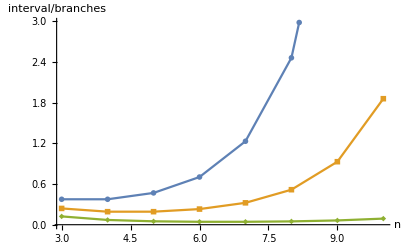

```mathematica
ListPlot[Drop[Table[Table[{n,(int/bra)},{n,3,10}],{km,3,6}],{-2}], AxesLabel->{"n","interval/branches"},PlotMarkers->{Automatic,Large}, Joined->True]
```

#### Timing for probK

In this example, calculating numerical values using a series expansion is much faster than direct differentiation with probK.  However, direct differentiation is slower for algebraic values.

Note: The example gf, sl, is calculated in the first single-deme example below

```mathematica
sl⟦1⟧
```

1/((6+ω[{a}]+ω[{b}]+ω[{c}]+ω[{d}]) (3+ω[{a}]+ω[{b}]+ω[{c,d}]) (1+ω[{a}]+ω[{b,c,d}]))

```mathematica
Timing[tbl=Array[probK[
DeleteCases[MapThread[If[#2==#3+1,Null,{#1,#2}]&,
{configs,{##},{3,3,3,3,3,3}}],Null],sl⟦1⟧,ω,0.2]&,{5,5,5,5,5,5},0];]
```

{3.61533,Null}

```mathematica
Timing[cl=Array[(0.1)^(Total[{##}]-1)&,{4,4,4,4,4,4},0]CoefficientList[Series[sl⟦1⟧/.{ω[x_List]:>(0.1-δ[x])},Sequence@@({δ[#],0,3}&/@configs)],δ/@configs];]
```

{0.44947,Null}

```mathematica
Timing[tbl=Array[probK[
DeleteCases[MapThread[If[#2==#3+1,Null,{#1,#2}]&,
{configs,{##},{3,3,3,3,3,3}}],Null],sl⟦1⟧,ω,θ]&,{5,5,5,5,5,5},0];]
```

{4.95011,Null}

```mathematica
Timing[cl=Array[(θ/2)^(Total[{##}]-1)&,{4,4,4,4,4,4},0]CoefficientList[Series[sl⟦1⟧/.{ω[x_List]:>(θ/2-δ[x])},Sequence@@({δ[#],0,3}&/@configs)],δ/@configs];]
```

{11.75333,Null}

#### Beyond infinite-sites: the Jukes-Cantor model

The notebook assumes infinite-sites mutation.  With deep coalescence events and high mutation rates, back-mutation needs to be considered. Probabilities can still be derived from the GF, but the number of mutational configurations becomes very large, unless some further simplification is made.

The probability of seeing j differences with n sites is (Eq. 2 of Lohse et al. 2011):

P[j]=(3/4)^n(n
j)∑_(k=0)^j ∑_(a=k)^(n-j+k) (-1)^k(1/3)^(n-j-a+k)(j
k)(n-j
a-k)ψ[μa]= (3/4)^n(n
j)∑_(a=0)^n (-9)^(a+j-n)(j
n-a-j)(2a+j-n
n-j)ψ[μa]

This calculation would be much faster than the infinite-sites version, since it involves a sum, rather than derivatives.  However, it would not be easy to calculate the full probability with multiple branches, since one would need to allow for multiple states - for example, the probability of seeing four different states on four leaves. It is not obvious whether mutational configurations could be simplified enough to allow them to be counted.

#### MakePT1

```mathematica
MakePT1::usage="MakePT1[GF,ω,θ,{{a},{b}},{k_(m, a),k_(m, b)}] uses a series expansion to make a table of mutation numbers {0,(…k)_m} for each listed branch. MakePT1[GF,ω,θ,{{a},…},{{a},{b},…},{k_(m, a),k_(m, b)}] makes a sub-table that sums over the branches in the first list, by setting those ω to 0.  This sub-table is embedded in the larger table with dimension {0(…k)_(m, a)+1,0(…k)_(m, b)+1,}, where the last element represents the residual probability. ";
```

```mathematica
MakePT1[gf_,ω_,θ_,sl_List,km_List]:=Module[{δ},
Array[(θ/2)^Total[{##}]&,km+1,0]PadRight[CoefficientList[Series[gf/.{ω[x_List]:>((θ/2)-δ[x])},Sequence@@MapThread[{δ[#1],0,#2}&,{sl,km}]],δ/@sl],km+1]];
```

```mathematica
MakePT1[gf_,ω_,θ_,zl_List,fl_List,km_List]:=
Module[{ss=TakeAway[fl,zl],rls=(ω[#]:>0)&/@zl,pos},
pos=Flatten[Position[fl,#]&/@ss];
EmbedTable[MakePT1[gf/.rls,ω,θ,ss,km⟦pos⟧],pos,km+2,km+2]];
```

#### MakePT

```mathematica
MakePT::usage="MakePT[GF,ω,θ,{{a},{b},…},{k_(m, a),k_(m, b)}] uses a series expansion to make a table of mutation numbers {0,(…k)_m} for each listed branch, and adds the residual probability to the last element in each row. Thus, each row runs from 0,…,k_m+1. Uses adjustTable to set the last element to the residual probability. Note: This appears no faster than direct differentiation, imlemented as the default in MakeProbTable.";
```

```mathematica
MakePT[gf_,ω_,θ_,fl_List,km_Integer]:=MakePT[gf,ω,θ,fl,ConstantArray[km,Length[fl]]];
MakePT[gf_,ω_,θ_,fl_List,km_List]:=
Module[{mt,nc=Length[fl],tot,rls=(ω[#]:>0)&/@fl},
tot=gf/.rls;
mt=Total[MakePT1[gf,ω,θ,#,fl,km]&/@Subsets[fl,{0,nc-1}]];
adjustTable[ReplacePart[mt,(km+2)->tot],nc]];
```

To implement an efficient method:
	- For a given set of ω, a subset will be zero, and the remainder will be used to make a series expansion
	- This set is embedded into a SparseArray with the full dimension
	- The full table is built up accordingly

To be flexible, I need to define an arbitrary list of branches that are distinguished, and that are the ω in the full GF.  The list of k_m must correspond to this list.  Any particular GF depends on a subset of these branches.  On this subset, I define sets of zeros; the remainder are used to make a full coefficient list.  This has to be slotted into the correct position in the full table.  However, because adjustTable is needed, it is best to first build the subtable, and then the full table.

Note: The next section shows that this method does not seem any faster than direct differentiation,

#### EmbedTable

```mathematica
EmbedTable::usage="EmbedTable[{{…},…},{i_1,…},{j_1,…},{d_1,…}] embeds the given table in a larger SparseArray with dimensions {d_1,…}. {i_1,…} lists the positions of the table dimensions in the larger SparseArray, and {j_1,…} lists the positions of the remaining dimensions.  For convenience, j has the same length as d, but the dimensions replaced by the embedded table are disregarded. EmbedTable[{{…},…},{i_1,…},1,{d_1,…}] uses the default position 1 for all dimensions.";
```

```mathematica
EmbedTable[tbl_List,i:{___Integer},j_Integer,d:{__Integer}]:=
EmbedTable[tbl,i,ConstantArray[j,Length[d]],d];
EmbedTable[tbl_List,i:{___Integer},j:{___Integer},d:{__Integer}]:=
Module[{xx,pl},
xx=IntegerSets[Dimensions[tbl]];(* all the entries that will be tabulated; {1,1,…}…{Subscript[d, 1],Subscript[d, 2],…} *)
pl=(ReplacePart[j,MapThread[Rule,{i,#}]])&/@xx;(* lists all the assignments that will be used to build the array *)
SparseArray[pl->Flatten[tbl],d]
(* builds a SparseArray with higher dimension d than the original table *)];
```

Example: The 2×3 table is embedded in a 3×4×3 SparseArray, using dimensions {1,3}, and inserting into position 2 of the remaining dimensions:

```mathematica
EmbedTable[{{a,b,bb},{c,d,dd}},{1,3},{0,2,0},{3,4,3}]//Normal
```

{{{0,0,0},{a,b,bb},{0,0,0},{0,0,0}},{{0,0,0},{c,d,dd},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}}}

#### IntegerSets

This is actually just a flattened Array[List,k]

```mathematica
IntegerSets::usage="IntegerSets[{k_1,k_2,…}] makes a flat list of all combinations of integers {i_1,i_2,…} for 1≤i≤k.   ";
```

```mathematica
IntegerSets[k:{__Integer}]:=Flatten[Array[List,k],Length[k]-1];
```

#### MakeProbTableOnce

```mathematica
MakeProbTableOnce::usage="MakeProbTableOnce[{{ψ,…},…},ω[{a,b}],θ,k_max] is used by MakeProbTable[] to construct a table of probabilities of all mutational configurations.  It takes a GF, or a GF that has already been differentiated to give a partial table, and constructs a series expansion in ω[{a,b}] around θ/2.  Tabulates 0(…k)_max itations, and adds a final element that gives the residual probability.";
```

```mathematica
MakeProbTableOnce[gf_,ω_,θ_,km_Integer]:=Module[{cl,δ,tr=TensorRank[gf]},
If[tr==0,cl=(θ/2)^Range[0,km] PadRight[CoefficientList[Series[gf/.ω:>(θ/2-δ),{δ,0,km}],δ],km+1];
Append[cl,(gf/.ω:>0)-Total[cl]] (* appends the residual probability *),
Map[MakeProbTableOnce[#,ω,θ,km]&,gf,{tr}]
(* if gf is a table, applies the function to the deepest level *)]];
```

#### Comparing direct differentiation with a series expansion

There are two alternative methods: direct differentiation using probK, and another method using a series expansion.  Surprisingly, the series expansion is much slower when θ is given numerically.  This contrasts with the check above (see under probK), because here, I use MakeTableOnce to find the residual probability.  It seems that a series expansion will give numerical values faster, but I have not found a way to use this efficiency when the residual probabilities are calculated.

Note: The example gf, sl, is calculated in the first single-deme example below

```mathematica
sl2=1/((6+ω[{a}]+ω[{b}]+ω[{c}]+ω[{d}]) (3+ω[{a}]+ω[{c}]+ω[{b,d}]) (1+ω[{a}]+ω[{b,c,d}]));
```

```mathematica
br=Subsets[{a,b,c,d},{1,3}];
```

```mathematica
Timing[tblNew=MakeProbTable[sl2,ω,0.2,br,3,OldMethod->False];]
```

{28.6378,Null}

```mathematica
Timing[tblOld=MakeProbTable[sl2,ω,0.24,br,3];]
```

{4.55628,Null}

When θ is kept as a symbol, the series expansion fails altogether.  The direct method using probK is much slower:

```mathematica
Timing[tblNewθ=MakeProbTable[sl2,ω,θ,br,3,OldMethod->False];]
```

$Aborted

```mathematica
Timing[tblOldθ=MakeProbTable[sl2,ω,θ,br,3];]
```

{8.73943,Null}

The two methods do agree:

```mathematica
{18Total[#//Flatten]&/@{tblNew,tblOld,tblOldθ/.θ->0.2},{Min[tblNew-tblOld//Flatten],Max[tblNew-tblOld//Flatten]}}
```

{{1.,1.,1},{-5.83437×10^-14,6.53337×10^-14}}

Note:  It may take an unreasonably long time to replace θ by a numerical value. The above expression is fast, but Min[tblNew-(tblOldθ/.θ→0.2)] fails, for obscure reasons.  It may be that Mathematica sometimes tries to convert a SparseArray into an enormous normal expression.

```mathematica
Timing[tblSeriesθ=MakePT[sl2,ω,θ,GetConfigsGF[sl2,ω],3];]
```

{42.35534,Null}

```mathematica
Timing[tblSeries=MakePT[sl2,ω,0.2,GetConfigsGF[sl2,ω],3];]
```

{5.28017,Null}

MakeProbTable generates a big array, in this example with 14 dimensions.  To compare the values, the output fromMakePT must be embedded into a table with the same dimensions.

```mathematica
tblSeriesBig=EmbedTable[tblSeries//Normal,{1,2,3,4,9,14},1,ConstantArray[5,14]]
```

SparseArray[<15625>, {5, 5, 5, 5, 5, 5, 5, 5, 5, 5, 5, 5, 5, 5}]

Miraculously, the new method gives the correct values:

```mathematica
{Min[tblSeriesBig-tblOld//Flatten],Max[tblSeriesBig-tblOld//Flatten]}
```

{-7.62259×10^-17,7.23105×10^-17}

Summary: Three methods are implemented: direct differentiation (the default OldMethod->True in MakeProbTable); series expansion (OldMethod->True in MakeProbTable); and a more efficient series expansion scheme in MakePT.   The latter has about the same speed as direct differentiation for numerical θ, but is much slower for algebraic expressions.  However, I have not tested it extensively.

### Setting up tables of probabilities: main functions

#### likFullG

```mathematica
likFullG::usage="likFullG[gf,ω,θ,rlznum,max] uses CoefficeintList to tabulate the probabilities of mutational configurations of to max mutations. By default the table of probabilities has the same dimensions as the list of ω of the gf. However a specific subset of ωs can be specified in ωlist (other ω parameteres are then set to 0). If ωlist is empty likFullG computes the marginal probability";
```

```mathematica
likFullG[gf_,ω_,θ_,rlznum_List,max_Integer]:=likFullG[gf,ω,θ,rlznum, ConstantArray[max,GetConfigsGF[gf,ω]//Length]];
```

```mathematica
likFullG[gf_,ω_,θ_,rlznum_List, max_List]:=
likFullG[gf,ω,θ,rlznum,GetConfigsGF[gf,ω]//Sort,max];
```

```mathematica
likFullG[gf_,ω_,θ_,rlznum_List,ωlist_,max_Integer]:=likFullG[gf,ω,θ,rlznum,ωlist,ConstantArray[max,Length[ωlist]]];
```

```mathematica
likFullG[gf_,ω_,θ_,rlznum_List,ωlist_,max_List]:=Module[{rules, nc,δs,δsmax,δ},
rules=(ω[#]:>θ/2-δ[#])&/@ωlist;
nc=ωlist//Length;
δs=δ[#]&/@ωlist;
δsmax={#⟦1⟧,0,#⟦2⟧}&/@({δs,max}//Thread);

N[(If[ωlist=={},gf/.rlznum/.ω[_]->0,CoefficientList[(Series[gf/.rlznum/.rules/.ω[_]->0,##]&@@δsmax),δs]]×
Array[(θ/2)^Total[{##}]&,max+1,ConstantArray[0,nc]]),Infinity]];
```

Note: There is a peculiar singularity at θ=2; the likelihood calculation blows up at this value.

```mathematica
likFullG[twoEnRXTsimpSort⟦2⟧//Total,ω,2,{M->0,T->1.7},{},3]
```

0.0222488

#### probK

```mathematica
probK::usage="probK[{{{a},2},{{{b,c},3},…},ψ,ω,θ] gives the probability of 2 mutations ancestral to {a}, and 3 to {b,c}. If arguments are omitted, then the probability is summed over these classes.  If a table of all the probabilities is needed, it is more efficient to use MakeProbTable[].";
```

```mathematica
probK[skl:{{_List,_Integer}...},ψ_,ω_,θ_]:=Module[{kl,rls},
rls=(ω[#⟦1⟧]->θ/2)&/@skl;
kl=Last/@skl;
(-θ/2)^Total[kl]/(Times@@(kl!))(D[ψ,Sequence@@(skl/.{s_List,k_Integer}:>{ω[s],k})]/.rls/.{ω[_]:>0})];
```

Note: probK calculates the probability of a configuration k by differentiating k times. If a full table of probabilities is needed, then it might be more efficient to use Mathematica’s built-in series expansion, and extract the coefficients.  However, this is not straightforward.

#### MakeProbTable

```mathematica
MakeProbTable::usage="MakeProbTable[GF,ω,θ,branches,{k_(m, 1),…}] generates a sparse array that gives the probability of each possible mutation type. MakeProbTable[{GF,…},ω,θ,branches,{k_(m, 1),…}] generates a list of tables, all with the same dimensions. Generates a large sparse array, with dimensions ∏(2+k_(max, i)), where k_m defines the maximum number of mtations that are counted.  The last entry in each column gives the residual probability - that is, the index runs {0,,1,…,k_max,residual}.  This is calculated using adjustTable.  The table is arranged in the same order as the list of branches that is supplied. Replacing {k_(m, 1),…} by an integer, k_m, sets the same maximum number of loci across all branches. OldMethod→False] is a slower version that uses a series expansion rather than the default option of direct differentiation.";
```

```mathematica
OldMethod::usage="OldMethod is an option for MakeProbTable; OldMethod→False specifies that a series expansion, raher than direct differentiation using probK should be used (the default).";
```

```mathematica
Options[MakeProbTable]={OldMethod->True};
```

```mathematica
MakeProbTable::badList="The list `1` of maximum numbers of mutations must have length equal to the list of branches, `2`.";
```

```mathematica
MakeProbTable::badBranches="The branches represented in the GF, `1` are not a subset of the supplied list of brancheslist of branches, `2`.";
```

```mathematica
MakeProbTable[gf_,ω_,θ_,branches_List,km_Integer,opts___Rule]:=
MakeProbTable[gf,ω,θ,branches,ConstantArray[km,Length[branches]],opts];
MakeProbTable[gf_,ω_,θ_,branches_List,km:{__Integer},opts___Rule]:=
If[ListQ[gf],MakeProbTable[#,ω,θ,branches,km,opts]&/@gf,
Module[{configs=GetConfigsGF[gf,ω],posn,nc,tt},
If[Length[km]≠Length[branches],Message[MakeProbTable::badList,km,branches]];
If[!SubsetQ[branches,configs],Message[MakeProbTable::badBranches,configs,branches]];
posn=Flatten[Position[branches,#]&/@configs];
tt=If[OldMethod/.{opts}/.Options[MakeProbTable],
nc=Length[configs];(* number of configurations that appear in this GF *)
adjustTable[
Array[probK[
DeleteCases[MapThread[If[#2==#3+1,Null,{#1,#2}]&,
{configs,{##},km⟦posn⟧}],Null],gf,ω,θ]&,km⟦posn⟧+2,0],nc],
Fold[MakeProbTableOnce[#1,ω[#2⟦1⟧],θ,#2⟦2⟧]&,gf,Transpose[{configs,km⟦posn⟧}]]];EmbedTable[tt,posn,1,km+2]]];
```

#### configList

```mathematica
configList::usage="configList[t,k_max] generates a list of mutational configurations for a given list of maximum # of mutations per branch category, and a list of the position of each branch category. Used in likFullTab.";
```

```mathematica
configList[t_List,inc_,kmax_List]:=Module[{ll=Length[t],max=kmax⟦t⟧,cons,int},
If[t=={},{ReplacePart[kmax+1,(#->0)&/@inc]},
cons=ConstantArray[kmax+1,Times@@(max+1)];int=Flatten[Array[{##}&,max+1,ConstantArray[0,ll]],ll-1];ReplacePart[#,(#->0)&/@inc]&/@Table[ReplacePart[cons⟦k⟧,Table[t⟦i⟧->int⟦k,i⟧,{i,1,ll}]],{k,Length[int]}]]]
```

#### likFullTab

```mathematica
likFullTab::usage="likFullTab[GF,ω,θ,{m->m1,T1->t1...},k_max_List] generates a sparse array that gives the probability of k_i of each possible mutation type. The input is a nested list of GF terms, each corresponding to a different equivalence class. The list k_max gives the maximum number of mutations on each branch type. The output has dimensions Times@@(2+k_max). The number of branch types that the GF distinguishes (which must match the length of k_max) defines the number of types of mutations. The last entry in each column gives the residual probability - that is, the index runs {0,1,…,k_max,residual}.  This is calculated using adjustTable.  The table is arranged in the same order as the list of ω indices of the GF. likFullTab works regardless of whether the ω variables of the GF correpsond to rooted branches or to combinations of branches.";
```

```mathematica
likFullTab[gf_,ω_,θ_,rlznum_List,max_Integer]:=likFullTab[gf,ω,θ,rlznum,ConstantArray[max,GetConfigsGF[Total[gf],ω]//Length]];
```

```mathematica
likFullTab[gf_,ω_,θ_,rlznum_List,max_List]:=Module[{ngf,ωs,ωslen,ωsall,posωs,ncall,ωssub,incomp,posnincomp,maxsub,posn,liktab,pl,tbl},
ngf=Length[gf];
ωs=GetConfigsGF[#,ω]&/@gf(* number of configurations that appear in the GF for each equivalence class *);
ωslen=Length[#]&/@ωs(* number of ω terms in each equivalence class*);
ωsall=Flatten[ωs,1]//Union//Sort(* the total list of ω terms*);
posωs=Table[Flatten[Position[ωsall,#]&/@ωs⟦i⟧],{i,1,ngf}] ;
ncall=Length[ωsall];
ωssub=(Table[Subsets[#,{n}],{n,0,Length[#]}])&/@ωs;
incomp=Complement[ωsall,#]&/@ωs;
posnincomp=Table[Flatten[Position[ωsall,#]&/@incomp⟦i⟧],{i,1,ngf}] (* the position of incompatible branches. Needs testing for cases with multiple incompatible branches*);
posn=Table[Table[Flatten[Position[ωsall,#]&/@ωssub⟦i,k,o⟧],{o,1,Length[ωssub⟦i,k⟧]}],{i,1,ngf},{k,1,ωssub⟦i⟧//Length}](* pos'ns of the ω terms of each equivalence class in ωsall*);
liktab=Table[(likFullG[Total[Flatten[gf⟦i⟧]],ω,θ,rlznum,#⟦1⟧,max⟦#⟦2⟧⟧]&/@({ωssub⟦i,k⟧,posn⟦i,k⟧}//Thread)),{i,1,ngf},{k,1,ωssub⟦i⟧//Length}];
pl=Table[Flatten[Table[configList[#,posnincomp⟦i⟧,max]&/@posn⟦i,k⟧,{k,1,Length[ωssub⟦i⟧]}],2],{i,1,ngf}](* all the numbers of mutations that will be tabulated; {0,0,…}…{Subscript[k, max]+1,Subscript[k, max]+1,…} *);tbl=Table[SparseArray[(1+pl⟦i⟧)->Flatten[liktab⟦i⟧],max+2],{i,1,ngf}];Table[Fold[adjustTable[#1,ncall,#2]&,tbl⟦i⟧,posωs⟦i⟧],{i,1,ngf}]//Total];
```

#### totallnL

```mathematica
totallnL[gf_,ω_,θ_?NumberQ,rlznum_List,max_List,counts_SparseArray]:=Module[{probTab,posn},probTab=likFullTab[gf,ω,θ,rlznum,max];
posn=probTab["NonzeroPositions"];Total[Log[probTab["NonzeroValues"]]*(Extract[counts,#]&/@posn)]];
```

```mathematica
totallnL[gf_,ω_,θ_?NumberQ,rlznum_List,max_Integer,counts_SparseArray]:=totallnL[gf,ω,θ,rlznum,ConstantArray[max,GetConfigsGF[Total[gf],ω]//Length],counts];
```

#### totallnL2 (Non-numeric theta)

I have added the option that you specify a single max and this gets converted in likFullTab to the necessary list

```mathematica
totallnL2[gf_,ω_,θ_,rlznum_List,max_List,counts_SparseArray]:=Module[{probTab,posn},probTab=likFullTab[gf,ω,θ,rlznum,max];
posn=probTab["NonzeroPositions"];Total[Log[probTab["NonzeroValues"]]*(Extract[counts,#]&/@posn)]];
```

```mathematica
totallnL2[gf_,ω_,θ_,rlznum_List,max_Integer,counts_SparseArray]:=totallnL2[gf,ω,θ,rlznum,ConstantArray[max,GetConfigsGF[Total[gf],ω]//Length],counts]
```

Single deme (needs brackets around the gf for likFullTab)

```mathematica
totallnL2[{gf_},ω_,θ_,rlznum_List,max_List,counts_SparseArray]:=Module[{probTab,posn},probTab=likFullTab[{gf},ω,θ,rlznum,max];
posn=probTab["NonzeroPositions"];Total[Log[probTab["NonzeroValues"]]*(Extract[counts,#]&/@posn)]];
```

```mathematica
totallnL2[{gf_},ω_,θ_,rlznum_List,max_Integer,counts_SparseArray]:=totallnL2[{gf},ω,θ,rlznum,ConstantArray[max,GetConfigsGF[Total[gf],ω]//Length],counts]
```

#### adjustTable

```mathematica
adjustTable::usage="adjustTable[{{…},…},d] takes a table with dimension d in which the last element at each level is the total probability, and produces a table in which the last element is the residual probability.  This new table should sum to 1. adjustTable[{{…},…},d,k] makes the adjustment only for level k.  Note that d cannot be inferred from the depth of the table, because its elements may themselves have depth. Works with sparse arrays.";
```

```mathematica
adjustTable[t:(_List|_SparseArray),d_Integer,k_Integer]:=Module[{jj,nt},
jj=RotateRight[Range[d],k-1];nt=Transpose[t,jj];
Transpose[ReplacePart[nt,-1->(nt⟦-1⟧-Total[Drop[nt,-1]])],Normal[SparseArray[jj->Range[d]]]]];
```

```mathematica
adjustTable[t:(_List|_SparseArray),d_Integer]:=Module[{nt=t,j},
Do[nt=adjustTable[nt,d,j],{j,d}];nt];
```

```mathematica
adjustTable[t:(_List|_SparseArray),d_Integer,k_Integer]:=Module[{jj,nt},
jj=RotateRight[Range[d],k-1];nt=Transpose[t,jj];
Transpose[ReplacePart[nt,-1->(nt⟦-1⟧-Total[Drop[nt,-1]])],Normal[SparseArray[jj->Range[d]]]]];
```

```mathematica
?Transpose
```

RowBox[{"Transpose", "[", StyleBox["list", "TI"], "]"}] transposes the first two levels in StyleBox["list", "TI"]. 
RowBox[{"Transpose", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] transposes StyleBox["list", "TI"] so that the StyleBox["k", "TI"]SuperscriptBox["", "th"] level in StyleBox["list", "TI"] is the SubscriptBox[StyleBox["n", "TI"], StyleBox["k", "TI"]]SuperscriptBox["", "th"] level in the result.

```mathematica
Transpose[ReplacePart[nt,-1->(nt⟦-1⟧-Total[Drop[nt,-1]])],Normal[SparseArray[jj->Range[d]]]]
```

Part::partd: Part specification nt ⟦ -1 ⟧ is longer than depth of object.

Drop::normal: Nonatomic expression expected at position 1 in Drop[nt, -1].

Range::range: Range specification in Range[d] does not have appropriate bounds.

SparseArray::pos: The left-hand side of jj → Range[d] in {jj → Range[d]} is not a position or pattern that will match a position.

Transpose::list: List expected at position 2 in nt, TagBox[SparseArray[jj → Range[d]], False, Rule[Editable, False], Rule[SelectWithContents, True]].

Transpose[nt,SparseArray[jj→Range[d]]]

```mathematica
ReplacePart[nt,-1->(nt⟦-1⟧-Total[Drop[nt,-1]])]
```

Part::partd: Part specification nt ⟦ -1 ⟧ is longer than depth of object.

Drop::normal: Nonatomic expression expected at position 1 in Drop[nt, -1].

nt

```mathematica
{4,1,2,3}->Range[4]
```

{4,1,2,3}→{1,2,3,4}

```mathematica
SparseArray[{4,1,2,3}->{1,2,3,4}]
```

SparseArray[<4>, {4}]

```mathematica
Normal[SparseArray[{4,1,2,3}->Range[4]]]
```

{2,3,4,1}

```mathematica
RotateRight[Range[4],2-1]
```

{4,1,2,3}

#### Comparing MakeProbTable with likFullTab and MakePT

```mathematica
branch1=GetConfigsGF[twoEnRXTsimpSort⟦1⟧,ω];
branchall=GetConfigsGF[twoEnRXTsimpSort,ω];
```

It is unclear to me why likFullTab is more efficient than MakeProbTable. This tabulates probabilities under a strict divergence model with a global k_max=3 for blocks with fixed differences only.

```mathematica
AbsoluteTiming[ttKL1=likFullTab[{twoEnRXTsimpSort⟦1⟧//Flatten//Total},ω,2.48,{M->0.2,T->0.37},{3,3,3}];]
```

{5.61139,Null}

The default method used in MakeProbTable is much slower:

```mathematica
AbsoluteTiming[ttNB1=MakeProbTable[(twoEnRXTsimpSort⟦1⟧//Flatten//Total)/.{M->0.2,T->0.37},ω,2.48,branch1,3];]
```

{71.5256,Null}

Using Series expansion in MakeProbTable is almost as fast as likFullTab. I do not understand the difference between these  two functions ...

```mathematica
AbsoluteTiming[ttNB1b=MakeProbTable[(twoEnRXTsimpSort⟦1⟧//Flatten//Total)/.{M->0.2,T->0.37},ω,2.48,branch1,3,OldMethod->False];]
```

{9.94259,Null}

Both schemes give the same answer:

```mathematica
SetPrecision[Chop[(ttNB1-ttKL1)//Normal],2]//TableForm
```

0
0
0
0
0 | 0
0
0
0
0 | 0
0
0
0
0 | 0
0
0
0
0 | 0
0
0
0
0
0
0
0
0
0 | 0
0
0
0
0 | 0
0
0
0
0 | 0
0
0
0
0 | 0
0
0
0
0
0
0
0
0
0 | 0
0
0
0
0 | 0
0
0
0
0 | 0
0
0
0
0 | 0
0
0
0
0
0
0
0
0
0 | 0
0
0
0
0 | 0
0
0
0
0 | 0
0
0
0
0 | 0
0
0
0
0
0
0
0
0
0 | 0
0
0
0
0 | 0
0
0
0
0 | 0
0
0
0
0 | 0
0
0
0
0

but maybe differ in rounding error :

```mathematica
(ttNB1//Normal)-(ttKL1//Normal)//TableForm
```

-1.38778×10^-17
-3.46945×10^-17
-3.46945×10^-17
3.46945×10^-18
7.63278×10^-17 | 3.46945×10^-18
1.38778×10^-17
4.0766×10^-17
2.34188×10^-17
-4.85723×10^-17 | -1.9082×10^-17
1.56125×10^-17
-9.54098×10^-17
7.84962×10^-17
2.56739×10^-16 | -2.77556×10^-17
-2.68882×10^-17
1.52222×10^-16
-2.76255×10^-16
3.40006×10^-16 | 2.77556×10^-17
7.77156×10^-16
4.01068×10^-15
1.94605×10^-13
-1.99979×10^-13
-1.38778×10^-17
-4.51028×10^-17
1.02349×10^-16
-2.02095×10^-16
1.73472×10^-16 | -2.25514×10^-17
2.42861×10^-17
-3.90313×10^-17
1.87784×10^-16
9.71445×10^-17 | -3.81639×10^-17
2.25514×10^-17
-7.54605×10^-17
5.72459×10^-17
5.30825×10^-16 | -4.25007×10^-17
3.51282×10^-17
1.2902×10^-16
-1.76833×10^-16
4.57967×10^-16 | 2.84495×10^-16
2.59168×10^-15
1.49152×10^-14
3.41838×10^-13
-3.60725×10^-13
-3.1225×10^-17
1.56125×10^-17
-1.68268×10^-16
-3.85976×10^-17
2.32453×10^-16 | -1.73472×10^-17
1.73472×10^-18
4.33681×10^-18
3.90313×10^-18
-4.16334×10^-17 | -7.80626×10^-18
-9.97466×10^-18
1.4138×10^-16
-1.87784×10^-16
-2.84495×10^-16 | -5.24754×10^-17
1.06252×10^-17
-1.01264×10^-16
-9.52472×10^-17
4.91794×10^-16 | 5.20417×10^-16
5.7454×10^-15
4.34444×10^-14
6.96548×10^-13
-7.4666×10^-13
-2.94903×10^-17
-2.08167×10^-17
-1.25767×10^-17
-6.76542×10^-17
4.89192×10^-16 | -4.59702×10^-17
1.73472×10^-18
-7.7412×10^-17
-5.81132×10^-17
8.39606×10^-16 | -6.80879×10^-17
1.20563×10^-16
-1.85832×10^-16
-4.55907×10^-17
1.24206×10^-15 | -6.02816×10^-17
8.73867×10^-17
7.00937×10^-17
3.20382×10^-16
8.38739×10^-16 | 6.14092×10^-16
3.59782×10^-15
1.75667×10^-14
2.84288×10^-13
-3.09418×10^-13
4.16334×10^-17
-1.21431×10^-15
-1.05367×10^-14
-4.61749×10^-14
5.73847×10^-14 | -3.40006×10^-16
-2.64372×10^-15
-2.13562×10^-14
-5.70533×10^-14
8.06716×10^-14 | -3.60822×10^-16
-2.86576×10^-15
-1.61607×10^-14
-1.7139×10^-13
1.89416×10^-13 | -4.82253×10^-16
-4.13385×10^-15
-3.16015×10^-14
-2.40736×10^-13
2.75434×10^-13 | -2.42861×10^-16
-3.16067×10^-14
-4.94969×10^-13
-6.27554×10^-12
6.80701×10^-12

```mathematica
Total[Flatten[#]]&/@{ttNB1,ttKL1}
```

{0.670859,0.670859}

#### Comparing likFullTab with the old scheme

The probabilities of full configurations agree:

```mathematica
klOLD=quadfullNum[{2.43,0.37,0},3];
```

```mathematica
SetPrecision[klOLD⟦1,1⟧,2]//TableForm
```

2.4

```mathematica
klNEW=likFullTab[{twoEnRXTsimpSort⟦1⟧//Flatten//Total},ω,2.43,{M->0,T->0.37},{3,3,3}];
```

```mathematica
SetPrecision[Transpose[klNEW⟦1;;4,1;;4,1;;4⟧,{2,3,1}],2]//TableForm
```

0.021
0.019
0.015
0.011 | 0.019
0.014
0.0094
0.0066 | 0.015
0.0094
0.0055
0.0034 | 0.011
0.0066
0.0034
0.0017
0.018
0.013
0.0091
0.0067 | 0.013
0.0075
0.0046
0.0031 | 0.0091
0.0046
0.0024
0.0014 | 0.0067
0.0031
0.0014
0.00068
0.013
0.0078
0.0048
0.0032 | 0.0078
0.0043
0.0024
0.0015 | 0.0048
0.0024
0.0012
0.00066 | 0.0032
0.0015
0.00066
0.00031
0.0089
0.005
0.0028
0.0017 | 0.005
0.0027
0.0014
0.00079 | 0.0028
0.0014
0.00072
0.00037 | 0.0017
0.00079
0.00037
0.00017

```mathematica
SetPrecision[Transpose[ttNB1⟦1;;4,1;;4,1;;4⟧,{2,3,1}],2]//TableForm
```

0.021
0.019
0.015
0.011 | 0.019
0.014
0.0094
0.0066 | 0.015
0.0094
0.0055
0.0034 | 0.011
0.0066
0.0034
0.0017
0.018
0.013
0.0091
0.0067 | 0.013
0.0075
0.0046
0.0031 | 0.0091
0.0046
0.0024
0.0014 | 0.0067
0.0031
0.0014
0.00068
0.013
0.0078
0.0048
0.0032 | 0.0078
0.0043
0.0024
0.0015 | 0.0048
0.0024
0.0012
0.00066 | 0.0032
0.0015
0.00066
0.00031
0.0089
0.005
0.0028
0.0017 | 0.005
0.0027
0.0014
0.00079 | 0.0028
0.0014
0.00072
0.00037 | 0.0017
0.00079
0.00037
0.00017

The residual probs for AA_BB topologies also agree:

```mathematica
SetPrecision[oldD2=klOLD⟦2,1⟧,2]//TableForm
```

Part::partd: Part specification quadfullNum[{2.43, 0.37, 0}, 3] ⟦ 2, 1 ⟧ is longer than depth of object.

Part::partd: Part specification quadfullNum[{2.4, 0.37, 0}, 3.] ⟦ 2, 1 ⟧ is longer than depth of object.

quadfullNum[{2.4,0.37,0},3.]⟦2,1⟧

```mathematica
SetPrecision[newD2={Drop[#,-1]&/@Drop[Transpose[klNEW,{2,3,1}]⟦-1⟧,-1],Drop[#,-1]&/@Drop[klNEW⟦-1⟧,-1],Drop[#,-1]&/@Drop[Transpose[klNEW,{3,1,2}]⟦-1⟧,-1]}//Normal,2]//TableForm
```

0.021
0.012
0.0061
0.0032 | 0.012
0.0063
0.0032
0.0016 | 0.0061
0.0032
0.0016
0.00077 | 0.0032
0.0016
0.00077
0.00036
0.03
0.017
0.0076
0.0033 | 0.017
0.0078
0.0032
0.0014 | 0.0075
0.0031
0.0013
0.00056 | 0.003
0.0012
0.00048
0.00022
0.03
0.017
0.0075
0.003 | 0.017
0.0078
0.0031
0.0012 | 0.0076
0.0032
0.0013
0.00048 | 0.0033
0.0014
0.00056
0.00022

```mathematica
SetPrecision[oldD1={klOLD⟦3,1⟧},2]//TableForm
```

Part::partw: Part 3 of quadfullNum[{2.43, 0.37, 0}, 3] does not exist.

Part::partw: Part 3 of quadfullNum[{2.4, 0.37, 0}, 3.] does not exist.

quadfullNum[{2.4,0.37,0},3.]⟦3,1⟧

```mathematica
SetPrecision[newD1={Transpose[klNEW,{2,3,1}]⟦-1,-1⟧,klNEW⟦-1,-1⟧,Transpose[klNEW,{3,1,2}]⟦-1,-1⟧}//Normal,2]//TableForm
```

0.0039 | 0.0019 | 0.00083 | 0.00036 | 0.0003
0.0027 | 0.001 | 0.00041 | 0.00019 | 0.0003
0.0039 | 0.0019 | 0.00083 | 0.00036 | 0.0003

### Simplifying genealogies

#### unRoot

```mathematica
unRoot::usage="unRoot[gf,ω] relabels the ω variables of a GF to eliminate the root. Each ω corresponding to a branch of an unrooted genealogy is labeled by the two sets of leaves on either side - for example, a new variable ω[{{a},{b,c,d}}] is generated that replaces ω[{a}] and ω[{b,c,d}]";
```

```mathematica
unRoot[gf_,ω_]:=Module[{rω,rall,rcomp},
rω=GetConfigsGF[gf,ω];
rall=rω//Flatten//Union;(* this may need to be changed to allow for genes that are themselves lists? *)
rcomp=Complement[rall,#]&/@rω;gf/.{(ω[#⟦1⟧]->ω[#⟦2⟧])&/@({rω,(Sort[#]&/@({rω,rcomp}//Thread))}//Thread)}]
```

### Making simulated data

#### makeSample

```mathematica
makeSample::usage="makeSample[probs,n] draws n random samples according to the table of probabilities, and tabulates them in a sparse array that has the same form as the supplied table of probabilities.  probs may be a list or a sparse array.";
```

```mathematica
makeSample[pt:(_SparseArray|_List),n_]:=Module[{rls=ArrayRules[pt]},
SparseArray[(#⟦1⟧->#⟦2⟧)&/@Tally[RandomChoice[rls⟦All,2⟧->(rls⟦All,1⟧),n]]]];
```

### Summarising real data

#### replaceMax

```mathematica
replaceMax::usage="replaceMax[l_List,{max_,pos_}] replaces mutation counts > k_max with k_max+1. This function is needed for configcounts. ";
```

```mathematica
replaceMax[l_List,{max_,pos_}]:=Join[ReplacePart[#,pos->max+1]&/@(Select[l,#⟦pos⟧>max&]),Select[l,#⟦pos⟧⩽max&]];
```

#### configCounts

Note: configcounts works for arbitrary sample sizes. It is worthwhile to do this data summarizing step outside of Mathematica when dealing with large datasets or counting mutational configurations repeatedly, e.g. in sliding windows.

```mathematica
configCounts::usage="configcounts[l,max] counts blockwise mutational configurations for arbitrary number of mutation types. The input is a list of counts of those types in all blocks which should have the same ordering as the sorted list of ω terms of the GF. max is either a list of maxima or a single global maximum for all mutation types";
```

```mathematica
configCounts[l_List,max_List]:=Module[{ll=Length[max],r,truncl,maxt=max+1,counts},
r={max,Range[1,ll]}//Thread;truncl=Fold[replaceMax[#1,#2]&,l,r];
counts=((#⟦1⟧+1)->#⟦2⟧)&/@Tally[truncl];
SparseArray[counts,max+2]];
```

```mathematica
configCounts[l_List,max_Integer]:=configCounts[l,ConstantArray[max,Length[l⟦1⟧]]];
```

#### FindkMax

Note: Hard coded for 4 types, need to generalize to any # of branch types.

```mathematica
FindkMax::usage="For a given threshold p and a dataset consiting of a list of blockwise counts l, FindkMax[l,p] gives the kmax for each branch type such that (%l >k_max)<p. The output is a vector of kmax values and the total fraction of blocks > k_max.";
```

```mathematica
FindkMax[l_List,p_]:=Module[{ll=l⟦1⟧//Length,cond,kmax},
cond=Table[Sort[Select[(#⟦i⟧)&/@l,#>0&]],{i,1,ll}];kmax=Table[cond⟦i,-Round[Length[cond⟦i⟧]*p]⟧,{i,1,ll}];{kmax,(Select[l,#⟦1⟧>kmax⟦1⟧||#⟦2⟧>kmax⟦2⟧||#⟦3⟧>kmax⟦3⟧||#⟦4⟧>kmax⟦4⟧&]//Length)/(l//Length)//N}]
```